```mathematica
Quit
```

## MC Values (from Jess)

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/MC Results"];
```

```mathematica
mcmcFiles=<|"Model 1"->"mcmc_parameter_summary_model_1_20000steps.csv","Model 2"->"mcmc_parameter_summary_model_2_20000steps.csv","Model 3"->"mcmc_parameter_summary_model_3_50000steps.csv"|>;
```

```mathematica
(*Load raw MCMC observables.eps is NOT stored as an independent parameter-it is derived from (q0,j0) via the closure relation.eps_mean from the CSV is kept only as "epsMC" for cross-checking.*)BuildModelParamRanges[file_String]:=Module[{data,header,rows},data=Import[file,"Data"];
header=First[data];
rows=Rest[data];
Association[Map[Function[row,Module[{assocFull,datasetName,mkRange},assocFull=AssociationThread[header->row];
datasetName=assocFull["dataset"];
mkRange[base_String]:=Module[{mean,plusErr,minusErr},mean=assocFull[base<>"_mean"];
plusErr=assocFull[base<>"_plus"];
minusErr=assocFull[base<>"_minus"];
<|"mean"->mean,"min"->mean-minusErr,"max"->mean+plusErr|>];
datasetName-><|"q0"->mkRange["q0"],"j0"->mkRange["j0"],"Om0"->mkRange["Om0"],"epsMC"->mkRange["eps"]|>]],rows]]];
```

```mathematica
paramRanges3=BuildModelParamRanges[mcmcFiles["Model 3"]];
allParams=Association[KeyValueMap[Function[{modelName,file},modelName->BuildModelParamRanges[file]],mcmcFiles]];
```

```mathematica
AvailableModels[]=Keys[allParams];
AvailableDatasets[model_String]:=Keys[allParams[model]];
```

```mathematica
planckDatasets={"Planck","Planck + Union3","Planck + Pantheon+","Planck + DESY5","Planck + Union3 + Pantheon+ + DESY5"};
```

## Equations

```mathematica
zPlot=10;
zinitial=1000;
```

#### Defining the system of equations

```mathematica
dx= (1+z)x'[z]-(x[z]^2-x[z](2+q[z])-2-2q[z]+3Ω[z])==0;
dΩ=(1+z)Ω'[z]-Ω[z](x[z]+1-2q[z])==0;
dq=(1+z)q'[z]- (j[z]-q[z]-2 q[z]^2)==0;
dj= (1+z)j'[z]- (-s[z]-j[z](2+3q[z]))==0;
ds=(1+z)s'[z]- (-l[z]-s[z](3+4q[z]))==0;
dEh=(1+z)Eh'[z]- Eh[z](1+q[z])==0;
dH=(1+z)H'[z]- H[z](1+q[z])==0;
```

Autonomous system of equations
N=-ln(1+z) -> (1+z)d/dz = -d/dN

```mathematica
dxn= x'[n]+(x[n]^2-x[n](2+q[n])-2-2q[n]+3Ω[n])==0;
dΩn=Ω'[n]+Ω[n](x[n]+1-2q[n])==0;
dqn=q'[n]+ (j[n]-q[n]-2 q[n]^2)==0;
djn= j'[n]+ (-s[n]-j[n](2+3q[n]))==0;
dsn=s'[n]+ (-l[n]-s[n](3+4q[n]))==0;
dEhn=Eh'[n]+ Eh[n](1+q[n])==0;
dHn=H'[n]+ H[n](1+q[n])==0;
```

```mathematica
Fx[x_,Ω_,q_]:=-(x^2-x (2+q)-2-2 q+3 Ω);
FΩ[x_,Ω_,q_]:=-Ω (x+1-2 q);
Fq[q_,j_]:=-(j-q-2 q^2);
```

#### Models of j

```mathematica
j0Func[z_]=1;
j1[z_]=1+3ϵ(1+q[z]);
j2[z_]=1+ϵ;
j3[z_]=1+3ϵ(q[z]-1/2);
```

```mathematica
(*Map model name->jModel function*)
jModelMap=<|"Model 0"->j0Func,"Model 1"->j1,"Model 2"->j2,"Model 3"->j3|>;
```

#### Determing ϵ from j0

```mathematica
EpsFast["Model 0",q0_?NumericQ,j0_?NumericQ]:=0;
EpsFast["Model 1",q0_?NumericQ,j0_?NumericQ]:= (j0-1)/(3(q0+1));
EpsFast["Model 2",q0_?NumericQ,j0_?NumericQ]:=-1+j0;EpsFast["Model 3",q0_?NumericQ,j0_?NumericQ]:= (j0-1)/(3(q0-1/2));
```

```mathematica
(*Using for module checking*)
epsValModel0=EpsFast["Model 0",allParams["Model 3"]["Planck + Union3","q0","mean"],allParams["Model 3"]["Planck + Union3","j0","mean"]]
epsValModel3=EpsFast["Model 3",allParams["Model 3"]["Planck + Union3","q0","mean"],allParams["Model 3"]["Planck + Union3","j0","mean"]]
```

0

-0.0149176

### Modules for DE solving

```mathematica
SolveForEh[model_String,dataset_String]:=
Module[{params,qFn,odeEh,sol,ϵVal, q0Val, j0Val},
params=allParams[model,dataset];
qFn=SolveForq[model,dataset];
q0Val=params[ "q0", "mean"];
j0Val=params[ "j0", "mean"];
ϵVal=EpsFast[model,q0Val_?NumericQ,j0Val_?NumericQ];

odeEh={(dEh/. q->qFn/.{ϵ->ϵVal, q0->q0Val}),Eh[0]==1};
sol=NDSolve[odeEh,Eh,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
Eh/. sol[[1]]];
```

```mathematica
SolveForq[model_String,dataset_String]:=
Module[{params,odeQ,sol,q0Val,j0Val,epsVal},
params=allParams[model,dataset];
q0Val=params["q0","mean"];
j0Val=params["j0","mean"];

epsVal=EpsFast[model,q0Val,j0Val];
odeQ={dq/. j->jModelMap[model]/. {ϵ->epsVal,q0->q0Val,j0->j0Val},q[0]==q0Val};

sol=NDSolve[odeQ,q,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
q/. sol[[1]]];
```

## Phase Space Analysis:

## Determining stability of fixed points

#### General fixed points for each model and specified dataset

```mathematica
FixedPointsStability[model_String,dataset_String]:=
Module[{params,epsVal,q0Val,j0Val,jExpr,jAlg,fps,Jac,classify,stabilityGrid},
params=allParams[model,dataset];
q0Val=params[ "q0", "mean"];
j0Val=params[ "j0", "mean"];
epsVal=EpsFast[model,q0Val,j0Val];
jExpr=jModelMap[model][n];

Block[{ϵ},ϵ=epsVal;
jAlg=jExpr/. q[n]->q;(*turn into algebraic expression in q*)
fps=NSolve[{Fx[x,Ω,q]==0,FΩ[x,Ω,q]==0,Fq[q,jAlg]==0},{x,Ω,q},Reals];

Jac[x_,Ω_,q_]=D[{Fx[x,Ω,q],FΩ[x,Ω,q],Fq[q,jAlg]},{{x,Ω,q}}];

classify[pt_]:=Module[{vals,eig,type},vals={x,Ω,q}/. pt;
eig=Eigenvalues[Jac@@vals]//N;
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];
{vals,eig,type}];
stabilityGrid=Grid[Prepend[classify/@fps,{"(x*, Ω*, q*)","Eigenvalues","Type"}],Frame->All];];
<|"model"->model,"dataset"->dataset,"eps"->epsVal,"fixedPoints"->fps,"stabilityGrid"->stabilityGrid|>];
```

```mathematica
fixedPointResults=Association[Map[Function[model,model->Association[Map[#->FixedPointsStability[model,#]&,AvailableDatasets[model]]]],AvailableModels[]]];
```

### Matter dominated fixed points

#### Matter dominated fixed point selection modules

```mathematica
(* ============================================================*)
(*Extract the matter-dominated fixed point:the one closest to (x,Ω,q)=(0,1,1/2),the eps->0 EdS limit*)
(* ============================================================*)
ExtractMatterDominatedFP[fps_List]:=Module[{target,distances,bestIdx},
target={0,1,1/2};
distances=Map[Function[pt,Module[{vals},vals={x,Ω,q}/. pt;
Norm[N[vals]-N[target]]]],fps];
bestIdx=First[Ordering[distances,1]];
fps[[bestIdx]]];
```

```mathematica
MatterDominatedFP[model_String,dataset_String]:=
Module[{fpResult,fps,bestFP,vals,eig,eigvecs,type,Jac,jAlg,epsVal},
fpResult=FixedPointsStability[model,dataset];

fps=fpResult["fixedPoints"];
epsVal=fpResult["eps"];
bestFP=ExtractMatterDominatedFP[fps];
vals={x,Ω,q}/. bestFP;

Block[{ϵ},ϵ=epsVal;
jAlg=jModelMap[model][n]/. q[n]->q;
Jac[xx_,OOmega_,qq_]=D[{Fx[xx,OOmega,qq],FΩ[xx,OOmega,qq],Fq[qq,jAlg]},{{xx,OOmega,qq}}];
{eig,eigvecs}=Eigensystem[Jac@@vals]//N;];
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];

<|"model"->model,"dataset"->dataset,"eps"->epsVal,"x"->vals[[1]],"Ω"->vals[[2]],"q"->vals[[3]],"eigenvalues"->eig,"eigenvectors"->eigvecs,"type"->type|>];
```

```mathematica
matterDominatedFPs=Association[Map[Function[model,model->Association[Map[#->MatterDominatedFP[model,#]&,AvailableDatasets[model]]]],AvailableModels[]]];
```

#### Model 3 results

```mathematica
Grid[Prepend[Table[{dataset,{matterDominatedFPs["Model 3"][dataset]["x"],matterDominatedFPs["Model 3"][dataset]["Ω"],matterDominatedFPs["Model 3"][dataset]["q"]},matterDominatedFPs["Model 3"][dataset]["eigenvalues"],matterDominatedFPs["Model 3"][dataset]["type"]},{dataset,AvailableDatasets["Model 3"]}],{"Dataset","{x*,Ω*,q*}","Eigenvalues","Type"}],Frame->All]
```

Dataset | {x*,Ω*,q*} | Eigenvalues | Type
DESI | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Union3 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Pantheon+ | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Union3 + Pantheon+ + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Union3 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Pantheon+ | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Union3 + Pantheon+ + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle

## Background Analysis

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/Background results"];
```

## Obtaining Background cosmographic solutions

### Obtaining q(z)

```mathematica
AvailableDatasets["Model 3"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
qSolAllSets1=Association[Map[#->SolveForq["Model 1",#]&,AvailableDatasets["Model 1"]]];
qSolAllSets2=Association[Map[#->SolveForq["Model 2",#]&,AvailableDatasets["Model 2"]]];
```

```mathematica
qSolAllSets3=Association[Map[#->SolveForq["Model 3",#]&,AvailableDatasets["Model 3"]]];
qSolPlanckSets3=Association[Map[#->SolveForq["Model 3",#]&,planckDatasets]];
```

```mathematica
qAssocByModel=<|"Model 1"->qSolAllSets1,"Model 2"->qSolAllSets2,"Model 3"->qSolAllSets3|>;
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/Background analysis results"];
DumpSave["qallModels.mx",{qAssocByModel}];
SetDirectory@NotebookDirectory[];
```

#### Model 3, Planck datasets

```mathematica
PlotQ[model_String,opts:OptionsPattern[]]:=Module[{qa,dsets},
qa=qAssocByModel[model];
dsets=Keys[qa];
Plot[Evaluate[Table[qa[d][z],{d,dsets}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[dsets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotRange->All,PlotLabel->model,GridLines->Automatic,ImageSize->600]];
```

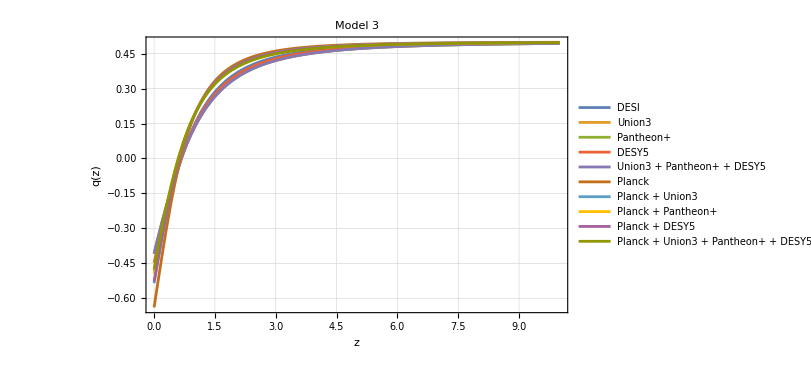

```mathematica
PlotQ["Model 3"]
```

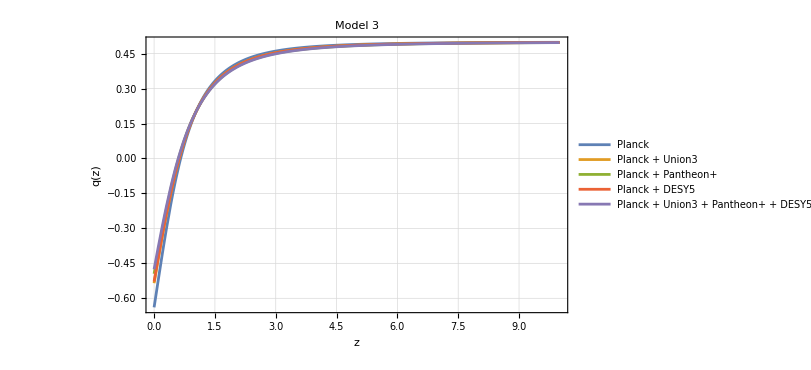

```mathematica
Plot[Evaluate[Table[qSolPlanckSets3[d][z],{d,Keys[qSolPlanckSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolPlanckSets3],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotRange->All,PlotLabel->"Model 3",GridLines->Automatic,ImageSize->600]
```

### Obtaining E(z)

```mathematica
ESolAllSets1=Association[Map[#->SolveForEh["Model 1",#]&,AvailableDatasets["Model 1"]]];
ESolAllSets2=Association[Map[#->SolveForEh["Model 2",#]&,AvailableDatasets["Model 2"]]];
```

```mathematica
ESolAllSets3=Association[Map[#->SolveForEh["Model 3",#]&,AvailableDatasets["Model 3"]]];
ESolPlanckSets3=Association[Map[#->SolveForEh["Model 3",#]&,planckDatasets]];
```

```mathematica
EAssocByModel=<|"Model 1"->ESolAllSets1,"Model 2"->ESolAllSets2,"Model 3"->ESolAllSets3|>;
```

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/Background analysis results"];
DumpSave["EallModels.mx",{EAssocByModel}];
SetDirectory@NotebookDirectory[];
```

#### Model 3, All datasets

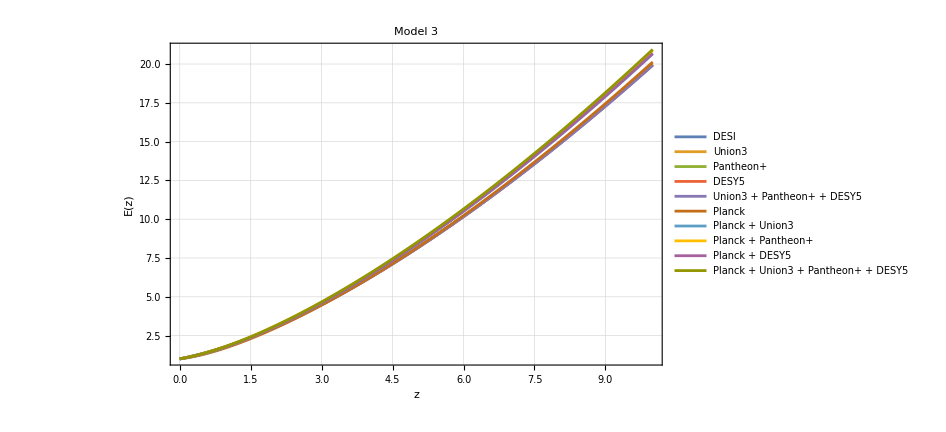

```mathematica
Plot[Evaluate[Table[ESolAllSets3[d][z],{d,Keys[ESolAllSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[ESolAllSets3],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.38,0.8}],Frame->True,FrameLabel->{"z","E(z)"},PlotLabel->"Model 3",PlotRange->All,GridLines->Automatic,ImageSize->700]
```

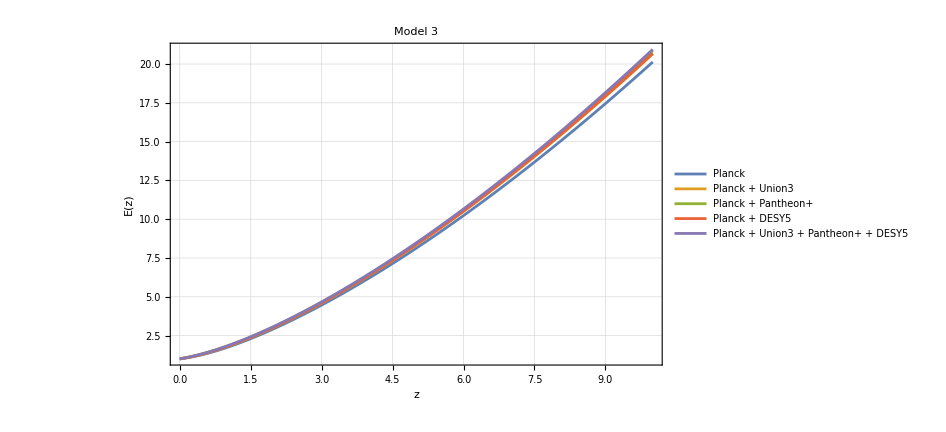

```mathematica
Plot[Evaluate[Table[ESolPlanckSets3[d][z],{d,Keys[ESolPlanckSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[ESolPlanckSets3],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.38,0.8}],Frame->True,FrameLabel->{"z","E(z)"},PlotLabel->"Model 3",PlotRange->All,GridLines->Automatic,ImageSize->700]
```

### Matter density (Ω_m) Analysis (MCMC values)

```mathematica
EAssocByModel["Model 1",viablePlanckDatasets[[1]]]
```

Part::partd: Part specification viablePlanckDatasets⟦1⟧ is longer than depth of object.

Missing[KeyAbsent,viablePlanckDatasets⟦1⟧]

#### Modules

```mathematica
SolveForOmegaM[model_String,dataset_String]:=
Module[{params,Om0,EhSol},
params=allParams[model,dataset];
Om0=params["Om0"]["mean"];
EhSol=EAssocByModel[model, dataset];
With[{Om0val=Om0},Function[zval,Om0val*(1+zval)^3/EhSol[zval]^2]]];
```

```mathematica
PlotOmegaM[model_String,OmegaMAllSetsModel_Association,zmax_:zPlot]:=Module[{datasets,colours,legend},datasets=Keys[OmegaMAllSetsModel];
colours=ColorData[97,"ColorList"][[1;;Length[datasets]]];
legend=LineLegend[colours,datasets,LegendMarkerSize->20,LegendFunction->(Framed[#,RoundingRadius->0,Background->White,FrameStyle->Gray]&)];
Plot[Evaluate[Table[OmegaMAllSetsModel[ds][z],{ds,datasets}]],{z,0,zmax},PlotStyle->colours,PlotLegends->Placed[legend,{1.05,0.5}],PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"z","Ω_m(z)"},PlotLabel->model,ImageSize->1000]];
```

#### Model 3

```mathematica
OmegaMAllSets3=Association[Map[#->SolveForOmegaM["Model 3",#]&,AvailableDatasets["Model 3"]]];
OmegaMPlanckSets3=Association[Map[#->SolveForOmegaM["Model 3",#]&,planckDatasets]];
```

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/Background analysis results"];
DumpSave["OmegaMAllSets3.mx",{OmegaMAllSets3}];
SetDirectory@NotebookDirectory[];
```

```mathematica
PlotOmegaM["Model 3",OmegaMAllSets3]
```

-Graphics-

```mathematica
PlotOmegaM["Model 3",OmegaMPlanckSets3]
```

-Graphics-

### DE equation of state

#### Modules

```mathematica
SolveForwDE[model_String,dataset_String,qSol_,OmegaMSol_]:=Module[{},Function[zval,(2*qSol[zval]-1)/(3*(1-OmegaMSol[zval]))]];
```

```mathematica
PlotwDE[model_String,wDEAllSetsModel_Association,datasets_List]:=Module[{colors,plotwDE},
colors=ColorData[97,"ColorList"][[1;;Length[datasets]]];
plotwDE=Plot[Evaluate[Table[wDEAllSetsModel[d][z],{d,datasets}]],{z,0,zPlot},PlotStyle->colors,PlotLegends->Placed[LineLegend[colors,datasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],Right],Frame->True,FrameLabel->{"z","w_DE(z)"},PlotLabel->model,GridLines->Automatic,PlotRange->Automatic,ImageSize->600];
plotwDE];
```

```mathematica
allParams["Model 3", "Planck"]
```

<|q0→<|mean→-0.638833,min→-0.742173,max→-0.531331|>,j0→<|mean→1.31132,min→1.03311,max→1.62362|>,Om0→<|mean→0.293759,min→0.279563,max→0.309709|>,epsMC→<|mean→-0.0911274,min→-0.167625,max→-0.0106933|>|>

#### Model 3:

```mathematica
wDEAllSets3=Association[Map[#->SolveForwDE["Model 3",#,qSolAllSets3[#],OmegaMAllSets3[#]]&,AvailableDatasets["Model 3"]]];
```

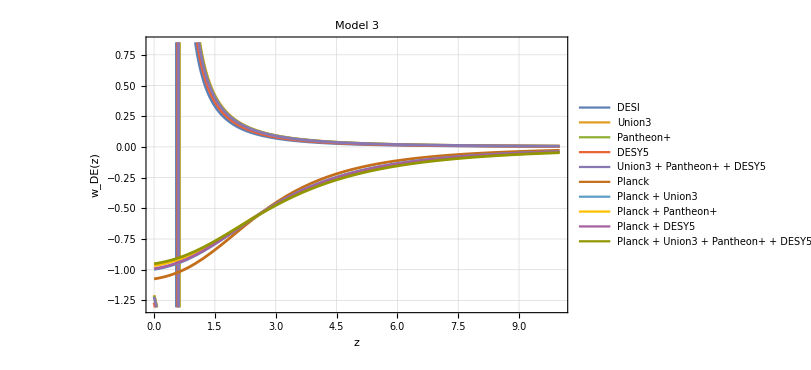

```mathematica
plotwDE3=PlotwDE["Model 3",wDEAllSets3,AvailableDatasets["Model 3"]]
```

```mathematica
wDEPlanckSets3=Association[Map[#->SolveForwDE["Model 3",#,qSolPlanckSets3[#],OmegaMPlanckSets3[#]]&,planckDatasets]];
```

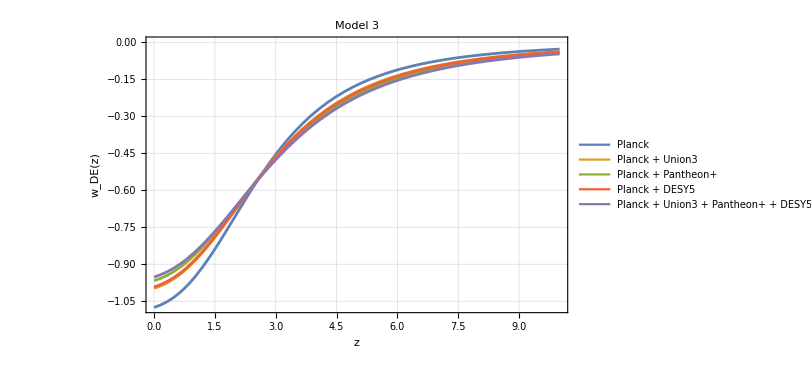

```mathematica
plotwDE3=PlotwDE["Model 3",wDEPlanckSets3,planckDatasets]
```

## Adding j=1 Model

#### Adding q0 vals

```mathematica
(*Using q0 values from Model 3 MCMC analysis for model 0*)
allParams["Model 0"]=Map[MapAt[Map[1&,#]&,#,{Key["j0"]}]&,allParams["Model 3"]];
```

### q(z)

```mathematica
qLCDMFunc[q0_?NumericQ]:=Module[{sol},
sol=Block[{j},j[zz_]:=1;
NDSolve[{dq,q[0]==SetPrecision[q0,40]},q,{z,0,zinitial},PrecisionGoal->20,AccuracyGoal->20,WorkingPrecision->40,MaxSteps->10^6]];
q/. sol[[1]]];
```

```mathematica
qAssocByModel["Model 0"]=Association[#->qLCDMFunc[allParams["Model 3"][#]["q0","mean"]]&/@Keys[allParams["Model 3"]]];
```

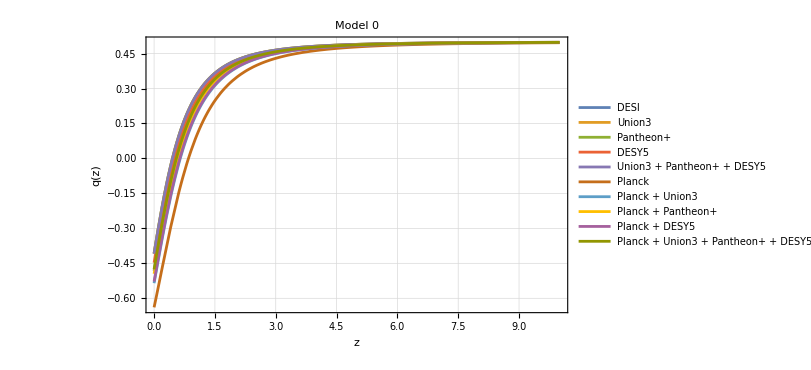

```mathematica
PlotQ["Model 0"]
```

## Determining physically viable x(z) and Ω(z) trajectories:

### Modules

#### Matter dominated fixed point selection modules

```mathematica
FixedPointsStabilityEps[model_String,epsVal_?NumericQ]:=Module[{jExpr,jAlg,fps,jacMat,jacFn,xx,OO,qq},
jExpr=jModelMap[model][n];
(*substitute onto private symbols:qq,xx,OO cannot collide with the global x,Ω,q used as ODE function names*)
jAlg=(jExpr/. q[n]->qq)/. ϵ->epsVal;
fps=NSolve[{Fx[xx,OO,qq]==0,FΩ[xx,OO,qq]==0,Fq[qq,jAlg]==0},{xx,OO,qq},Reals];
jacMat=D[{Fx[xx,OO,qq],FΩ[xx,OO,qq],Fq[qq,jAlg]},{{xx,OO,qq}}];
jacFn=Function[{xv,Ov,qv},jacMat/. {xx->xv,OO->Ov,qq->qv}];
<|"eps"->epsVal,"jAlg"->jAlg,"fixedPoints"->fps,"vars"->{xx,OO,qq},"Jac"->jacFn|>];
```

```mathematica
MatterDominatedFPEps[model_String,epsVal_?NumericQ]:=MatterDominatedFPEps[model,epsVal]=Module[{fpResult,fps,vars,Jac,ptVals,target,distances,bestIdx,vals,eig,eigvecs,type},fpResult=FixedPointsStabilityEps[model,epsVal];
fps=fpResult["fixedPoints"];vars=fpResult["vars"];
Jac=fpResult["Jac"];
ptVals=Map[N[vars/. #]&,fps];
target=N[{0,1,1/2}];
distances=Map[Norm[#-target]&,ptVals];
bestIdx=First[Ordering[distances,1]];
vals=ptVals[[bestIdx]];
{eig,eigvecs}=Eigensystem[Jac@@vals]//N;
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];
<|"model"->model,"eps"->epsVal,"jAlg"->fpResult["jAlg"],"x"->vals[[1]],"Ω"->vals[[2]],"q"->vals[[3]],"eigenvalues"->eig,"eigenvectors"->eigvecs,"type"->type|>];
```

```mathematica
MatterDominatedFPEps["Model 3", epsValModel3]
```

<|model→Model 3,eps→-0.0149176,jAlg→1-0.0447529 (-1/2+qq$13734),x→0.,Ω→1.,q→0.5,eigenvalues→{3.386,3.04475,-0.886001},eigenvectors→{{0.959049,-0.283239,0.},{-0.0551261,0.560767,0.826136},{0.663155,0.748482,0.}},type→Saddle|>

```mathematica
MatterDominatedFPEps["Model 0", epsValModel0]
```

<|model→Model 0,eps→0,jAlg→1,x→0.,Ω→1.,q→0.5,eigenvalues→{3.386,3.,-0.886001},eigenvectors→{{0.959049,-0.283239,0.},{6.75287×10^-17,0.5547,0.83205},{0.663155,0.748482,0.}},type→Saddle|>

#### Module to classify trajectory viability

```mathematica
(* Trajectory-wide viability classifier Condition:
x/(j-q-2)>=0  (assuming f_R>0),checked along the WHOLE trajectory 
denom = j-q-2;
	tol= 10^-3;
Checks:
1. abs(denom)< tol -> near singular -> denominator vanishing (point is near a fp or coordinate singluarity of (q,j)-> x map);
2. x/denom < 0 -> sign violation (unphysical);
3. Ω≤0 -> Omega violation (unphysical);
else: physical
*)

ClassifyTrajectoryViability[model_String,j0Val_?NumericQ,q0Val_?NumericQ,xFn_,ΩFn_,qFn_,zi_?NumericQ,OptionsPattern[{"NSamples"->150,"SingularTol"->10^-3,"ZMin"->10^-4,"MaxAbsX"->10^3,"MaxOmega"->10,"DomainTol"->10^-8}]]:=Module[{epsVal,nSamples,singTol,zMinSample,maxAbsX,maxOm,domainTol,domain,domainMin,domainMax,zSamples,sampleData,hasSignViolation,hasNearSingular,hasOmegaViolation,hasDivergence,isPhysical,label},
epsVal=EpsFast[model,q0Val,j0Val];
nSamples=OptionValue["NSamples"];
singTol=OptionValue["SingularTol"];
zMinSample=OptionValue["ZMin"];
maxAbsX=OptionValue["MaxAbsX"];
maxOm=OptionValue["MaxOmega"];
domainTol=OptionValue["DomainTol"];
domain=xFn["Domain"][[1]];
domainMin=domain[[1]];
domainMax=domain[[2]];
(*solution must actually reach z=0 and z=zi-- no extrapolation.DomainTol (strict) judges validity;ZMin only sets sample spacing below.*)If[domainMin>domainTol||domainMax<zi,Return[<|"label"->"Diverged","j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"domainMin"->domainMin,"domainMax"->domainMax,"sampleData"->{}|>]];
zSamples=Prepend[10^Subdivide[Log10[zMinSample],Log10[Min[zi,domainMax]],nSamples-2],0];
sampleData=Table[Module[{xVal,ΩVal,qVal,jVal,denom,ratio,pointLabel},xVal=xFn[zPt];
ΩVal=ΩFn[zPt];
qVal=qFn[zPt];
jVal=(jModelMap[model][zPt]/. ϵ->epsVal)/. q[zPt]->qVal;
denom=jVal-qVal-2;
pointLabel=Which[!(NumericQ[xVal]&&NumericQ[ΩVal]),"Divergent",Abs[xVal]>maxAbsX||ΩVal>maxOm,"Divergent",Abs[denom]<singTol,"NearSingular",ΩVal<=0,"OmegaViolation",xVal/denom<0,"SignViolation",True,"OK"];
ratio=If[Abs[denom]<singTol,Indeterminate,xVal/denom];
<|"z"->zPt,"x"->xVal,"Ω"->ΩVal,"q"->qVal,"j"->jVal,"denom"->denom,"ratio"->ratio,"pointLabel"->pointLabel|>],{zPt,zSamples}];
hasDivergence=AnyTrue[sampleData,#["pointLabel"]==="Divergent"&];
hasNearSingular=AnyTrue[sampleData,#["pointLabel"]==="NearSingular"&];
hasOmegaViolation=AnyTrue[sampleData,#["pointLabel"]==="OmegaViolation"&];
hasSignViolation=AnyTrue[sampleData,#["pointLabel"]==="SignViolation"&];
isPhysical=!(hasDivergence||hasNearSingular||hasOmegaViolation||hasSignViolation);
label=Which[isPhysical,"Physical",hasDivergence,"Divergent",hasNearSingular,"NearSingular",hasOmegaViolation,"OmegaViolation",hasSignViolation,"SignViolation"];
<|"label"->label,"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"hasDivergence"->hasDivergence,"hasSignViolation"->hasSignViolation,"hasNearSingular"->hasNearSingular,"hasOmegaViolation"->hasOmegaViolation,"minRatio"->Min[Cases[sampleData[[All,"ratio"]],_?NumericQ]],"minOmega"->Min[sampleData[[All,"Ω"]]],"maxOmega"->Max[sampleData[[All,"Ω"]]],"maxAbsX"->Max[Abs[sampleData[[All,"x"]]]],"minAbsDenom"->Min[Abs[sampleData[[All,"denom"]]]],"domainMin"->domainMin,"domainMax"->domainMax,"sampleData"->sampleData|>];
```

#### Classification of eigenvectors:

```mathematica
ClassifyEigenvectors[fp_Association]:=Module[{eig,vecs,unstableIdx,stableIdx,vq,vxOmega,qComponents},
eig=fp["eigenvalues"];
vecs=fp["eigenvectors"];
unstableIdx=Flatten[Position[eig,_?(Re[#]>0&)]];
stableIdx=Flatten[Position[eig,_?(Re[#]<0&)]];
qComponents=vecs[[unstableIdx,3]];
vq=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]];
vxOmega=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]];

vxOmega=If[vxOmega[[1]]<0,-vxOmega,vxOmega];
vq=If[vq[[3]]<0,-vq,vq];

<|"vq"->vq,"vxOmega"->vxOmega,"vStable"->vecs[[First[stableIdx]]],"lambdaQ"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]],"lambdaXOmega"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]]|>];
```

#### Scan of ICs

```mathematica
ScanICs[model_String,dataset_String,c2Range_List,zi_?NumericQ,OptionsPattern[{"NSamples"->80,"SingularTol"->10^-3,"PrecisionGoal"->14,"AccuracyGoal"->25,"MaxSteps"->10^8,"WorkingPrecision"->30}]]:=Module[{epsVal,j0Val,q0Val,nSamp,singTol,pg,ag,maxSt,wp,fp,cl,vq,vxOmega,qFn,deltaQ,c3,results},

j0Val=allParams[model, dataset, "j0", "mean"];
q0Val=allParams[model, dataset, "q0", "mean"];
epsVal=EpsFast[model,q0Val,j0Val];

nSamp=OptionValue["NSamples"];
singTol=OptionValue["SingularTol"];
pg=OptionValue["PrecisionGoal"];
ag=OptionValue["AccuracyGoal"];
maxSt=OptionValue["MaxSteps"];
wp=OptionValue["WorkingPrecision"];
fp=MatterDominatedFPEps[model,epsVal];
cl=ClassifyEigenvectors[fp];
If[cl===$Failed,Return[Table[<|"c2"->c2,"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"label"->"DegenerateFP"|>,{c2,c2Range}]]];
vq=cl["vq"];
vxOmega=cl["vxOmega"];
(*qFn=qSolPlanckSets3[ds];*)
qFn=qAssocByModel[model][dataset];

deltaQ=qFn[zi]-fp["q"];
c3=deltaQ/vq[[3]];
results=Table[Module[{xi,Ωi,sol,xFn,ΩFn,viability},
xi=SetPrecision[fp["x"]+c2 vxOmega[[1]]+c3 vq[[1]],wp];
Ωi=SetPrecision[fp["Ω"]+c2 vxOmega[[2]]+c3 vq[[2]],wp];

sol=Block[{q},q[zz_]:=qFn[zz];
Quiet[NDSolve[{dx,dΩ,x[zi]==xi,Ω[zi]==Ωi,WhenEvent[Abs[x[z]]>10^3,"StopIntegration"],WhenEvent[Ω[z]>10,"StopIntegration"],WhenEvent[Ω[z]<0,"StopIntegration"]},{x,Ω},{z,0,zi},PrecisionGoal->pg,AccuracyGoal->ag,MaxSteps->maxSt,WorkingPrecision->wp],{NDSolve::ndsz,NDSolve::mxst,NDSolve::precw,NDSolve::ndtol,NDSolve::nlnum,NDSolve::ndcf}]];

If[!MatchQ[sol,{{__Rule}}],<|"c2"->c2,"xi"->xi,"Ωi"->Ωi,"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"label"->"Failed"|>,(xFn=x/. sol[[1]];
ΩFn=Ω/. sol[[1]];
viability=ClassifyTrajectoryViability[model,j0Val,q0Val,xFn,ΩFn,qFn,zi,"NSamples"->nSamp,"SingularTol"->singTol];
Join[<|"c2"->c2,"xi"->xi,"Ωi"->Ωi|>,viability])]],{c2,c2Range}];
results];
```

#### Determine c2 range

```mathematica
AutoC2Scale[model_String,j0Val_?NumericQ,q0Val_?NumericQ,zi_?NumericQ]:=Module[{fp,classified},fp=MatterDominatedFPEps[model,EpsFast[model,q0Val,j0Val]];
classified=ClassifyEigenvectors[fp];
If[classified===$Failed,$Failed,(1+zi)^(-classified["lambdaXOmega"])]];
```

```mathematica
AutoC2Range[model_String,j0Val_?NumericQ,q0Val_?NumericQ,zi_?NumericQ,OptionsPattern[{"LogSpanBelow"->4,"LogSpanAbove"->2,"NPerSign"->40}]]:=Module[{scale,expMin,expMax,positive},scale=AutoC2Scale[model,j0Val,q0Val,zi];
If[scale===$Failed,Return[$Failed]];
expMin=Log10[scale]-OptionValue["LogSpanBelow"];
expMax=Log10[scale]+OptionValue["LogSpanAbove"];
positive=10^Subdivide[expMin,expMax,OptionValue["NPerSign"]-1];
Join[-Reverse[positive],positive]];
```

#### Determine physical results

```mathematica
(*helper:contiguous index runs of "Physical" points in a results list*)PhysicalRuns[results_List]:=Module[{idx},idx=Flatten[Position[results,r_/;r["label"]==="Physical",{1}]];
If[idx==={},{},Split[idx,#2==#1+1&]]];
```

```mathematica
(*(*default-zi overload*)
SweepXInitial[model_String,dataset_String,zinitial_,opts:OptionsPattern[]]:=SweepXInitial[model,dataset,zinitial,opts];*)
SweepXInitial[model_String,dataset_String,zi_?NumericQ,OptionsPattern[{"NCoarse"->100,"LogSpanBelow"->3,"LogSpanAbove"->2,"NRefine"->150,"NSamples"->80,"SingularTol"->10^-3,"PrecisionGoal"->14,"AccuracyGoal"->Infinity,"WorkingPrecision"->30}]]:=Module[{epsVal,j0Val,q0Val,nC,nR,nSamp,singTol,pg,ag,wp,coarseRange,nTot,coarseResults,runs,refined,allPts},

j0Val=allParams[model, dataset, "j0", "mean"];
q0Val=allParams[model, dataset, "q0", "mean"];
epsVal=EpsFast[model,q0Val,j0Val];

nC=OptionValue["NCoarse"];
nR=OptionValue["NRefine"];
nSamp=OptionValue["NSamples"];
singTol=OptionValue["SingularTol"];
pg=OptionValue["PrecisionGoal"];
ag=OptionValue["AccuracyGoal"];
wp=OptionValue["WorkingPrecision"];
coarseRange=AutoC2Range[model,j0Val,q0Val,zi,"NPerSign"->nC,"LogSpanBelow"->OptionValue["LogSpanBelow"],"LogSpanAbove"->OptionValue["LogSpanAbove"]];
If[coarseRange===$Failed,Return[<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->False,"nCoarse"->0,"nRefined"->0,"c2Window"->None,"windows"->{},"table"->{},"note"->"Degenerate fixed point"|>]];
nTot=Length[coarseRange];
coarseResults=ScanICs[model,dataset,coarseRange,zi,"NSamples"->nSamp,"SingularTol"->singTol,"PrecisionGoal"->pg,"AccuracyGoal"->ag,"WorkingPrecision"->wp];

runs=PhysicalRuns[coarseResults];
If[runs==={},Return[<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->False,"nCoarse"->0,"nRefined"->0,"c2Window"->None,"windows"->{},"table"->{},"note"->"No Physical points in coarse pass"|>]];
refined=Table[Module[{lo,hi,rng,res,phys},
lo=coarseRange[[Max[1,First[run]-1]]];
hi=coarseRange[[Min[nTot,Last[run]+1]]];
rng=Subdivide[lo,hi,nR-1];
res=ScanICs[model,dataset,rng,zi,"NSamples"->nSamp,"SingularTol"->singTol,"PrecisionGoal"->pg,"AccuracyGoal"->ag,"WorkingPrecision"->wp];
phys=Select[res,#["label"]==="Physical"&];
<|"bracket"->{lo,hi},"nPhysical"->Length[phys],"c2Window"->If[phys==={},None,MinMax[phys[[All,"c2"]]]],"points"->Map[<|"c2"->#["c2"],"xi"->#["xi"],"Ωi"->#["Ωi"],"xToday"->#["sampleData"][[1]]["x"],"ΩToday"->#["sampleData"][[1]]["Ω"]|>&,phys]|>],{run,runs}];
allPts=Flatten[refined[[All,"points"]],1];
<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->Length[allPts]>0,"nCoarse"->Total[Length/@runs],"nRefined"->Length[allPts],"nRuns"->Length[runs],"c2Window"->If[allPts==={},None,MinMax[allPts[[All,"c2"]]]],"windows"->refined[[All,"c2Window"]],"table"->allPts|>];
```

### Results for mean values of (j0, q0)

#### Raw

```mathematica
viablePlanckDatasets={"Planck + Union3","Planck + Pantheon+","Planck + DESY5","Planck + Union3 + Pantheon+ + DESY5"};
```

```mathematica
(*
sweepResultsByModel=<||>;
sweepResultsByModel["Model 3"]=AssociationMap[SweepXInitial["Model 3",#,zinitial]&,viablePlanckDatasets];
sweepResultsByModel["Model 0"]=AssociationMap[SweepXInitial["Model 0",#,zinitial]&,viablePlanckDatasets];
SetDirectory@NotebookDirectory[];
DumpSave["sweepResultsAllModels.mx",sweepResultsByModel];
*)
```

```mathematica
SetDirectory@NotebookDirectory[];
Get["sweepResultsAllModels.mx"];
```

#### Plots against x_i

```mathematica
MakeXOmegaTodayPlot[model_String,dataset_String,sweepResult_Association,opts:OptionsPattern[{ImageSize->350}]]:=Module[{table,xiVals,x0Vals,Omega0Vals},If[!sweepResult["found"]||sweepResult["table"]==={},Return[Graphics[Text["No viable points: "<>dataset],ImageSize->OptionValue[ImageSize]]]];
table=SortBy[sweepResult["table"],#["xi"]&];
xiVals=table[[All,"xi"]];
x0Vals=table[[All,"xToday"]];
Omega0Vals=table[[All,"ΩToday"]];
ListLinePlot[{Transpose[{xiVals,x0Vals}],Transpose[{xiVals,Omega0Vals}]},PlotLegends->Placed[LineLegend[{"x(0)","Ω(0)"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.2,0.2}],Frame->True,FrameLabel->{"x_i= x("<>ToString[zinitial]<>")",""},PlotRange->{-5,5},PlotLabel->model<>", "<>dataset,GridLines->Automatic,ImageSize->OptionValue[ImageSize],AspectRatio->1/2,PlotMarkers->{Automatic,Small}]];
```

```mathematica
xOmegaPlots=MakeXOmegaTodayPlot["Model 3",#,sweepResultsByModel["Model 3"][#]]&/@viablePlanckDatasets;
```

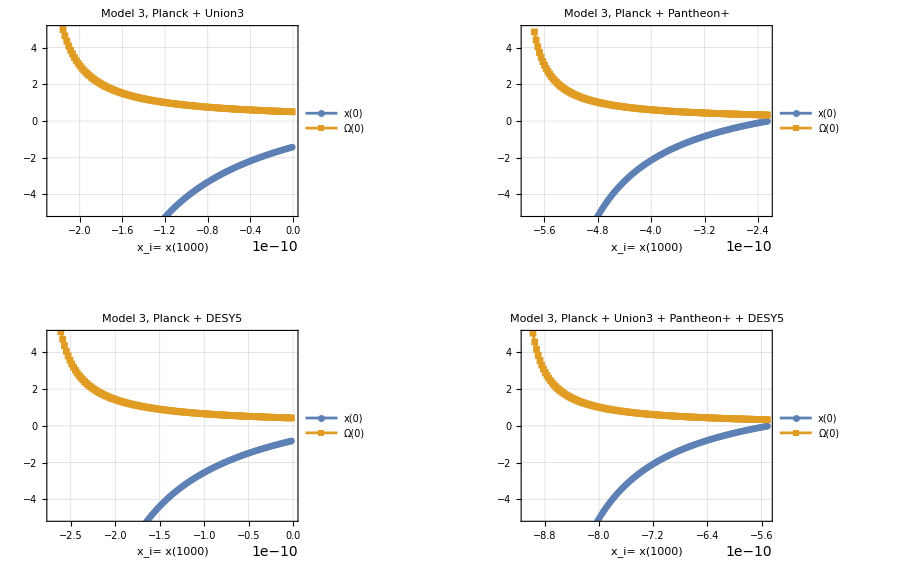

```mathematica
GraphicsGrid[Partition[xOmegaPlots,2],ImageSize->900,Spacings->{40,40}]
```

#### x_i plot model 0

```mathematica
xOmegaPlotsModel0=MakeXOmegaTodayPlot["Model 0",#,sweepResultsByModel["Model 0"][#]]&/@viablePlanckDatasets;
```

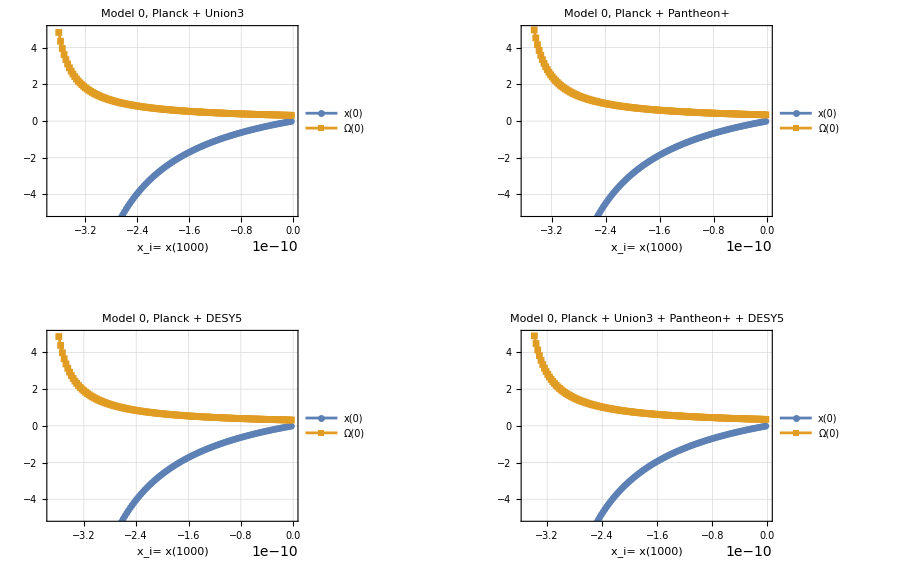

```mathematica
GraphicsGrid[Partition[xOmegaPlotsModel0,2],ImageSize->900,Spacings->{40,40}]
```

#### x_i plot comparing to model 0

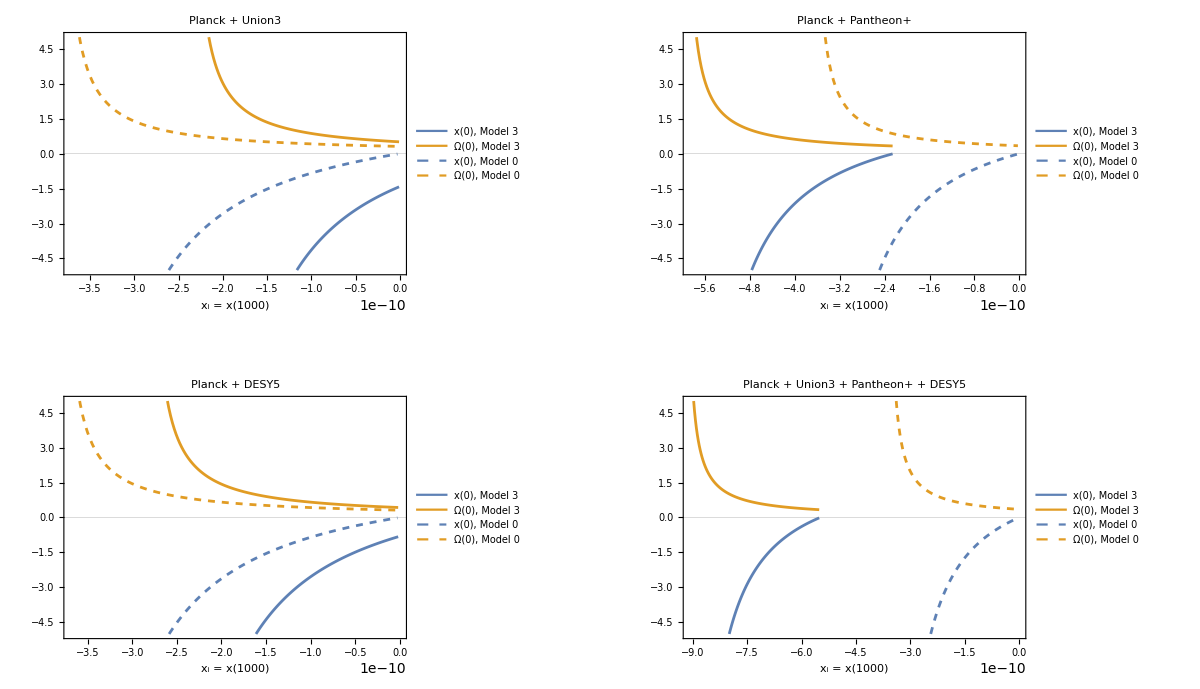

```mathematica
MakeXOmegaComparePlot[dataset_String,OptionsPattern[{ImageSize->600,"Models"->{"Model 3","Model 0"},"Dashing"->{{},{Small}}}]]:=Module[{models,dashes,sweeps,curves,styles,labels,colors},models=OptionValue["Models"];
dashes=OptionValue["Dashing"];
colors=ColorData[97,"ColorList"][[1;;2]];
sweeps=sweepResultsByModel[#][dataset]&/@models;
If[AnyTrue[sweeps,(!#["found"]||#["table"]==={})&],Return[Graphics[Text["No viable points: "<>dataset],ImageSize->OptionValue[ImageSize]]]];
curves=Flatten[MapThread[Function[{sw,m},Module[{tb},tb=SortBy[sw["table"],#["xi"]&];
{Transpose[{tb[[All,"xi"]],tb[[All,"xToday"]]}],Transpose[{tb[[All,"xi"]],tb[[All,"ΩToday"]]}]}]],{sweeps,models}],1];
styles=Flatten[MapThread[Function[{d,m},{Directive[colors[[1]],Dashing[d]],Directive[colors[[2]],Dashing[d]]}],{dashes,models}],1];
labels=Flatten[MapThread[Function[{m},{"x(0), "<>m,"Ω(0), "<>m}],{models}],1];
ListLinePlot[curves,PlotStyle->styles,PlotLegends->Placed[LineLegend[styles,labels,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LabelStyle->{FontSize->9}],{0.15,0.25}],Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(x\), \(i\)]\) = x("<>ToString[zinitial]<>")",""},PlotRange->{Automatic,{-5,5}},GridLines->{None,{{0,Directive[Gray,Thin]}}},PlotLabel->dataset,ImageSize->OptionValue[ImageSize],AspectRatio->1/2]];

xOmegaComparePlots=MakeXOmegaComparePlot/@viablePlanckDatasets;
GraphicsGrid[Partition[xOmegaComparePlots,2],ImageSize->1200,Spacings->{40,40}]
```

#### Evolution of x, Ω modules

```mathematica
nPoints=3;
xTodayThreshold=-1;
```

```mathematica
allSelected=<||>;
allPlots=<||>;
```

```mathematica
SelectEvenXi[sweepResult_Association,nPoints_Integer]:=Module[{filtered,xiVals,targets,idx},
filtered=Select[sweepResult["table"],#["xToday"]>=xTodayThreshold&];
If[filtered==={},Return[{}]];
filtered=SortBy[filtered,#["xi"]&];
xiVals=filtered[[All,"xi"]];
If[Length[filtered]<=nPoints,Return[filtered]];
targets=Subdivide[Min[xiVals],Max[xiVals],nPoints-1];
idx=DeleteDuplicates[First[Ordering[Abs[xiVals-#],1]]&/@targets];
filtered[[idx]]];
```

```mathematica
SolveBackground[model_String,dataset_String,calibratedICs_Association]:=Module[{params,qFn,zi,ic,xi,Ωi,qi,sol,xFn,ΩFn,domainEnd,wp,q0Val,j0Val},
ic=calibratedICs[dataset];
If[ic===$Failed||ic===None,Return[$Failed]];
wp=30;
params=allParams[model,dataset];
q0Val=params["q0","mean"];
j0Val=params["j0","mean"];

qFn=qAssocByModel[model][dataset];
zi=zinitial;
xi=SetPrecision[ic["xIn"],wp];
Ωi=SetPrecision[ic["OmegaIn"],wp];
qi=qFn[zinitial];

Block[{q,j,s,l,ϵ},
q[z_]=qFn[z];
ϵ=EpsFast[model,q0Val,j0Val];
j[z_]=jModelMap[model][z];
s[z_]=Solve[dj,s[z]][[1,1,2]];
l[z_]=Solve[ds,l[z]][[1,1,2]]//Simplify;
sol=Quiet[NDSolve[{dx,dΩ,x[zi]==xi,Ω[zi]==Ωi},{x,Ω},{z,0,zi},PrecisionGoal->14,AccuracyGoal->14,WorkingPrecision->wp],NDSolve::ndsz][[1]];
xFn=x/. sol;
ΩFn=Ω/. sol;];
domainEnd=xFn["Domain"][[1,1]];
If[domainEnd>0,Print[dataset," is stiff/diverges at z ≃ ",domainEnd]];
<|"x"->xFn,"Ω"->ΩFn,"q"->qFn,"z0"->0,"zinitial"->zinitial,"failedAtZ"->If[domainEnd>0,domainEnd,None],"xi"->xi,"Ωi"->Ωi,"qi"->qi|>];
```

```mathematica
PlotBackgroundSolutions[model_String,bgResults_Association,datasets_List]:=
Module[{colors,plotX,plotOmega},
colors=ColorData[97,"ColorList"][[1;;Length[datasets]]];

plotX=Plot[Evaluate[Table[bgResults[d]["x"][z],{d,datasets}]],{z,0,zPlot},PlotStyle->colors,PlotLegends->Placed[LineLegend[colors,datasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.5}],Frame->True,FrameLabel->{"z","x(z)"},GridLines->Automatic,PlotRange->All,ImageSize->650];
plotOmega=Plot[Evaluate[Table[bgResults[d]["Ω"][z],{d,datasets}]],{z,0,zPlot},PlotStyle->colors,PlotLegends->Placed[LineLegend[colors,datasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.5}],Frame->True,FrameLabel->{"z","Ω(z)"},GridLines->Automatic,PlotRange->All,ImageSize->650];

{plotX,plotOmega}];
```

#### Results

```mathematica
RunBackgroundForModel[model_String,datasets_List,OptionsPattern[{"NPoints":>nPoints,"Print"->True}]]:=Module[{nPts,doPrint,selectedAll,bgAll,plotsAll},nPts=OptionValue["NPoints"];
doPrint=OptionValue["Print"];
selectedAll=<||>;bgAll=<||>;plotsAll=<||>;
Do[Module[{selected,bgRes,xiLabels,checkTable,pX,pOmega},selected=SelectEvenXi[sweepResultsByModel[model][dataset],nPts];
selectedAll[dataset]=selected;
If[selected==={},If[doPrint,Print[Style[model<>", "<>dataset<>": no points with xToday >= "<>ToString[xTodayThreshold],Red]]],(*else*)bgRes=Association[Table[Module[{xi0,Omega0,label,calibratedICs,res},xi0=row["xi"];
Omega0=row["Ωi"];
label=Row[{Subscript["x","i"]," = ",ScientificForm[xi0,3]}];
calibratedICs=<|dataset-><|"xIn"->xi0,"OmegaIn"->Omega0|>|>;
res=SolveBackground[model,dataset,calibratedICs];
label->res],{row,selected}]];
bgAll[dataset]=bgRes;
xiLabels=Keys[bgRes];
{pX,pOmega}=PlotBackgroundSolutions[model,bgRes,xiLabels];
plotsAll[dataset]={pX,pOmega};
If[doPrint,checkTable=Grid[Prepend[MapThread[{#1["xi"],#1["Ωi"],#1["xToday"],bgRes[#2]["x"][0],#1["ΩToday"],bgRes[#2]["Ω"][0]}&,{selected,xiLabels}],{"xi","Ωi","xToday (sweep)","x(0) (NDSolve)","ΩToday (sweep)","Ω(0) (NDSolve)"}],Frame->All,Alignment->"."];
Print[Style[model<>", "<>dataset<>"  ("<>ToString[Length[selected]]<>" points)",Bold]];
Print[checkTable];Print[pX];Print[pOmega]]]],{dataset,datasets}];
<|"selected"->selectedAll,"bgResults"->bgAll,"plots"->plotsAll|>];
```

Model 3, Planck + Union3: no points with xToday >= -1

Model 3, Planck + Pantheon+  (3 points)

xi | Ωi | xToday (sweep) | x(0) (NDSolve) | ΩToday (sweep) | Ω(0) (NDSolve)
-3.32041×10^-10 | 1. | -0.9776238641668799384831799813 | -0.97661874196447182732250258679 | 0.45932647570508770310426262123 | 0.45919130734068434865859732732
-2.78929×10^-10 | 1. | -0.41298245279229468149371088082 | -0.41226151783987875424826222325 | 0.38339376271033176778846478851 | 0.38329681171482712750714835877
-2.25817×10^-10 | 1. | -0.008542374934609586446067700805 | -0.0079725728674020591684401374468 | 0.32900485014212113852227239145 | 0.32892822342601559237494410409

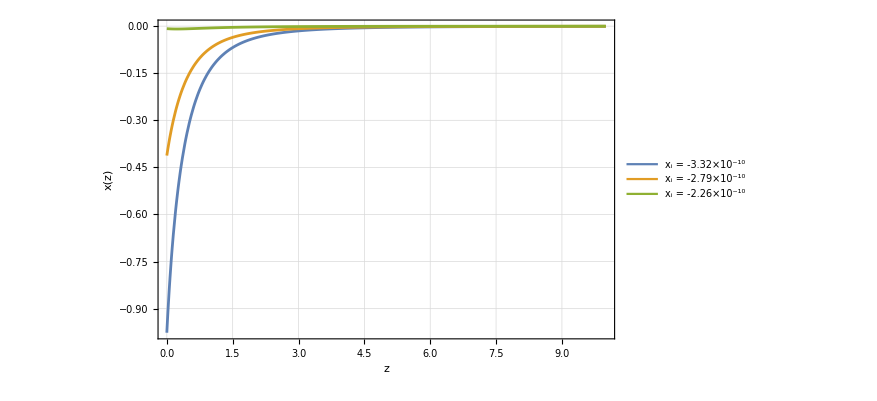

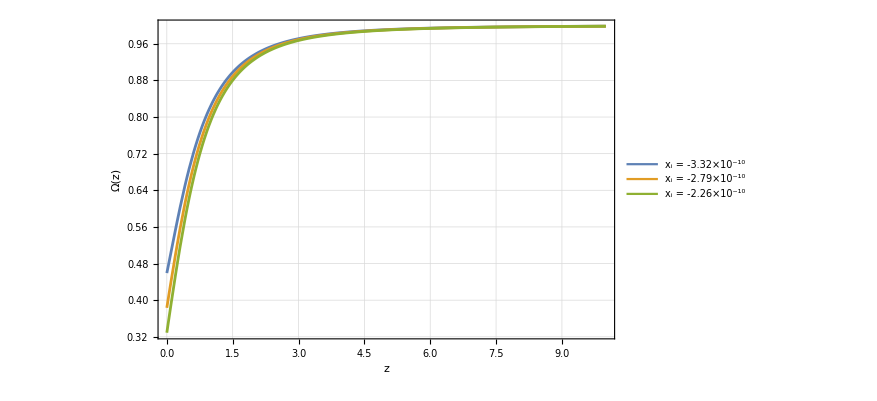

Model 3, Planck + DESY5  (3 points)

xi | Ωi | xToday (sweep) | x(0) (NDSolve) | ΩToday (sweep) | Ω(0) (NDSolve)
-1.63024×10^-11 | 1. | -0.99973429906582181325242902026 | -0.99873048148022629653611257177 | 0.45271866166169299870043591313 | 0.45258544210611832514779879498
-1.01284×10^-11 | 1. | -0.92308636225618808209861229279 | -0.92211928015522853248658908798 | 0.44254649083991811833738028883 | 0.44241814655823866455840650219
-1.89635×10^-12 | 1. | -0.82609184028055906459149123143 | -0.82518298010187669373551174599 | 0.42967406547109673956294918241 | 0.42955344799002636300051799572

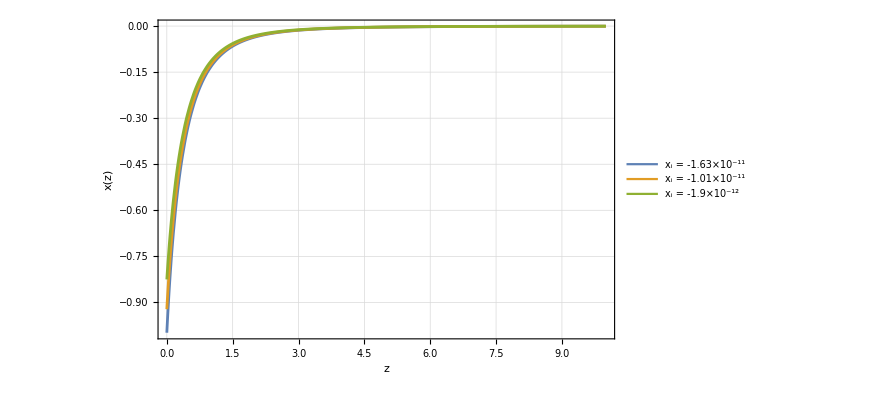

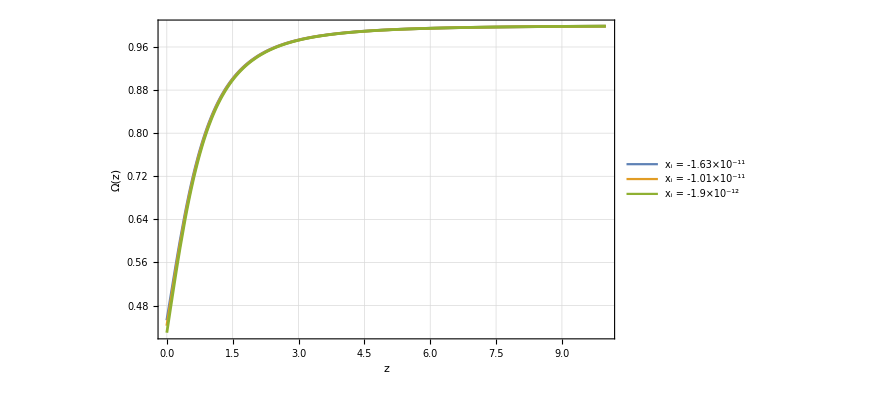

Model 3, Planck + Union3 + Pantheon+ + DESY5  (3 points)

xi | Ωi | xToday (sweep) | x(0) (NDSolve) | ΩToday (sweep) | Ω(0) (NDSolve)
-6.54715×10^-10 | 1. | -0.97100370638911977356400393139 | -0.97012912898638030495558175598 | 0.46371209818468884752198458013 | 0.46359365615689173362612952381
-6.0302×10^-10 | 1. | -0.41648112727954255961543526967 | -0.41582720792619467878739613498 | 0.38861436799309346761129871916 | 0.38852580918323178555283062489
-5.51325×10^-10 | 1. | -0.01653296426041379543816340422 | -0.016021672022716843622721720882 | 0.33445029899266113299353048216 | 0.33438105584874560666650049954

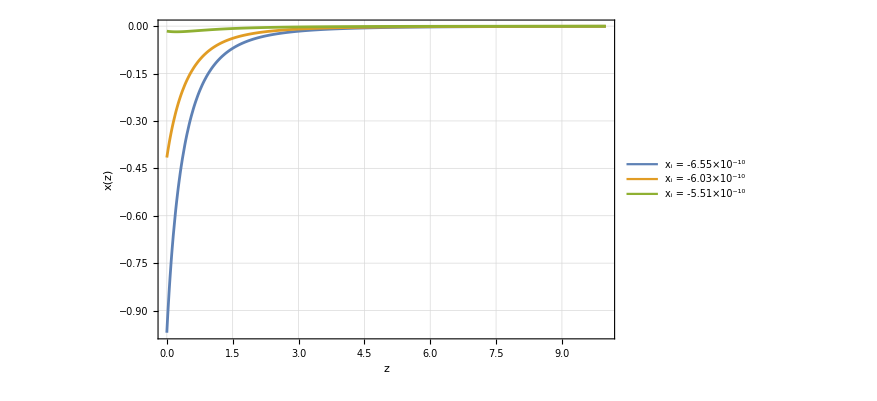

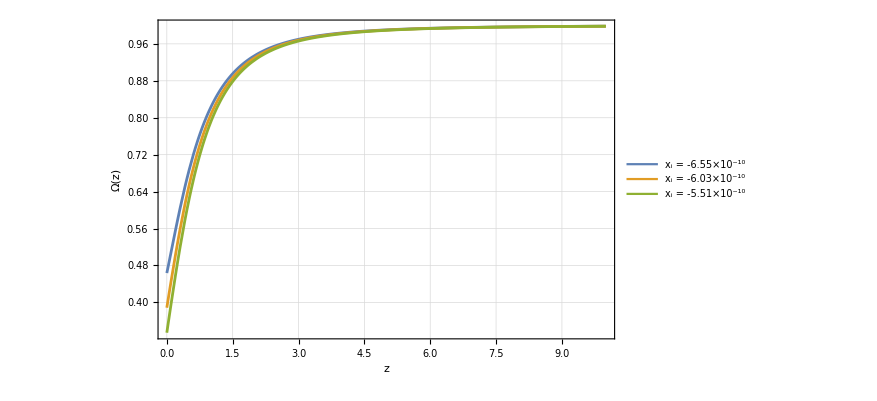

```mathematica
bgRun["Model 3"]=RunBackgroundForModel["Model 3",viablePlanckDatasets];
```

Model 0, Planck + Union3  (3 points)

xi | Ωi | xToday (sweep) | x(0) (NDSolve) | ΩToday (sweep) | Ω(0) (NDSolve)
-1.12113571927214964264911910715×10^-10 | 0.999999997813113328248846300994 | -0.98101573959593550322730255188 | -0.98013866784098182694930077538 | 0.43684306329963559225435773016 | 0.43672958627661518027646387841
-5.7391619465891759447258560411×10^-11 | 0.999999997796952255768587747298 | -0.41852670012494779240458142954 | -0.41787567437852461755240120002 | 0.36406728291909636113518202966 | 0.36398305210953627621508342091
-2.6696670045685651309215804089×10^-12 | 0.99999999778079096124372426857 | -0.016688426202861958590878180834 | -0.016182758770296133429529122903 | 0.31207676946997779570020335597 | 0.31201134536489180842077543917

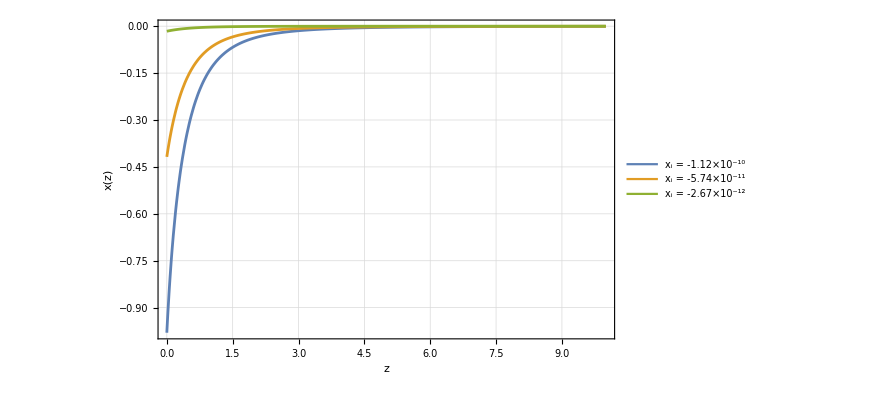

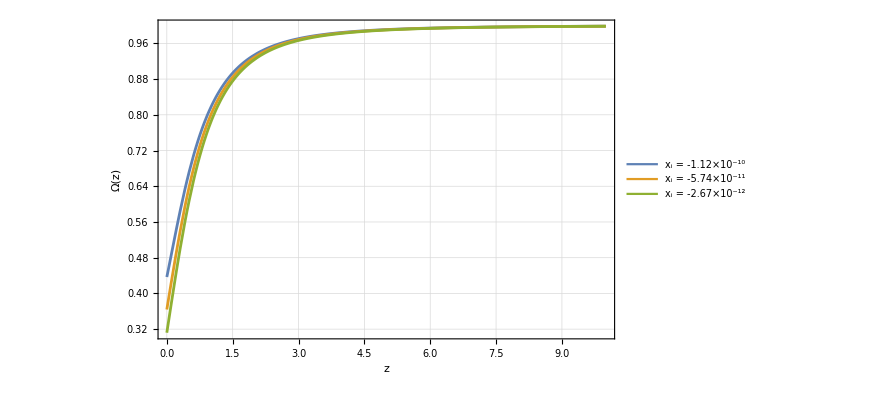

Model 0, Planck + Pantheon+  (3 points)

xi | Ωi | xToday (sweep) | x(0) (NDSolve) | ΩToday (sweep) | Ω(0) (NDSolve)
-1.07107199732011374015186198908×10^-10 | 0.999999998067826023628867915249 | -0.99395409742988170208862220776 | -0.99305756869919393732664149653 | 0.47342860134005725248917866278 | 0.47330530521671901237529128815
-5.35203845567568801629865360183×10^-11 | 0.999999998052000238502046158828 | -0.41282617657938075668525760962 | -0.41215876298253922366615677588 | 0.39350832972514379943878810659 | 0.39341654291824494099037733327
-2.36933370765030679743851003972×10^-12 | 0.999999998036893433805971653783 | -0.015739129726120411501187073041 | -0.015214055054966603585388851592 | 0.33889848652060608578847126389 | 0.33882627503529550621748651389

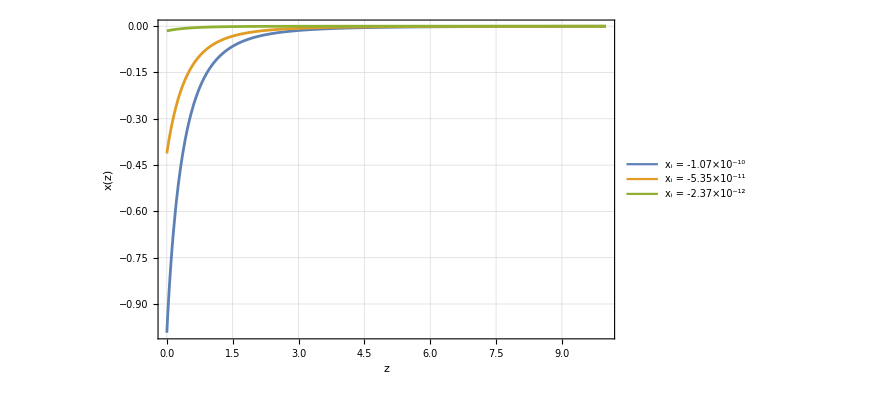

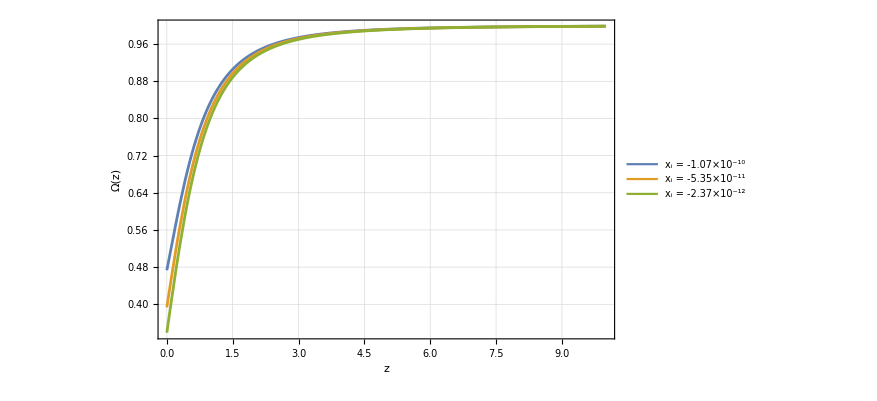

Model 0, Planck + DESY5  (3 points)

xi | Ωi | xToday (sweep) | x(0) (NDSolve) | ΩToday (sweep) | Ω(0) (NDSolve)
-1.12113571927214951340214839574×10^-10 | 0.999999997860612666045199148357 | -0.99478433081405648171423555455 | -0.99389902265205537988032175865 | 0.44468892782261540532414700569 | 0.44457312149575855366693117236
-5.73916194658917529849100248404×10^-11 | 0.999999997844451593564940594661 | -0.42368902069968056707432752702 | -0.42303278430925736561828898889 | 0.36998448833276201493617242205 | 0.36989864666815740131480294629
-2.66966700456855947636661178468×10^-12 | 0.999999997828290299040077115933 | -0.016874196090540275620035396831 | -0.016364989376802507491814042008 | 0.31676942438371843823328299239 | 0.31670281553306826929969087017

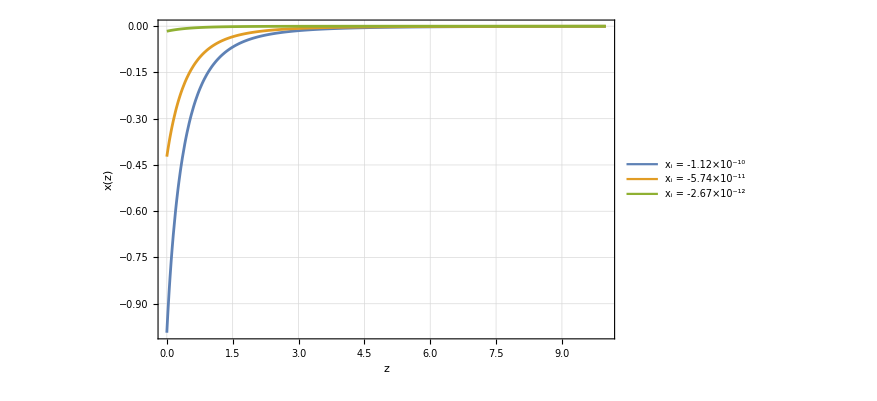

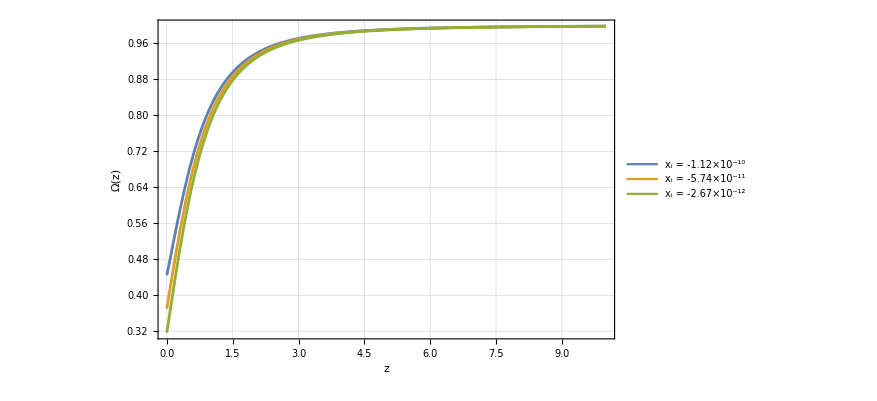

Model 0, Planck + Union3 + Pantheon+ + DESY5  (3 points)

xi | Ωi | xToday (sweep) | x(0) (NDSolve) | ΩToday (sweep) | Ω(0) (NDSolve)
-1.04671435405863437776560006544×10^-10 | 0.999999998176033577657051409915 | -0.99639098222496203025671364543 | -0.99550280810853011087154216334 | 0.49043776409647035488662183296 | 0.49031221844243571877744127938
-5.35203845567568672382894648772×10^-11 | 0.999999998160926995005581829901 | -0.42566885447708232997466802675 | -0.42499945140425295444018358049 | 0.4097647502480656470367112538 | 0.40967012843268201137791725839
-2.36933370765029346884465542551×10^-12 | 0.999999998145820190309507324855 | -0.016181883797276775798898009279 | -0.015656331245745508254619203151 | 0.35188273297476543211702772509 | 0.35180844479442815548360794804

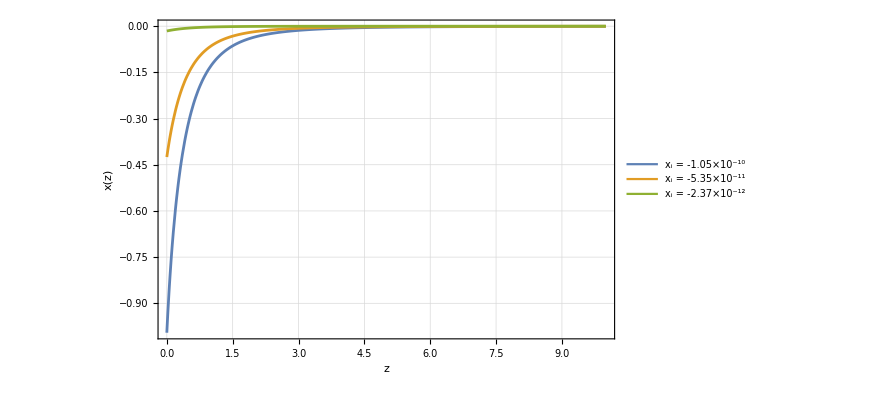

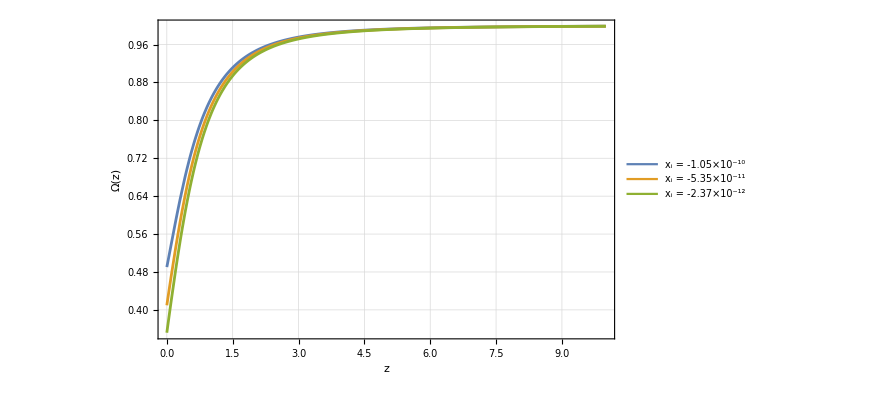

```mathematica
bgRun["Model 0"]=RunBackgroundForModel["Model 0",viablePlanckDatasets];
```

#### Saving results

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/Background analysis results"];
DumpSave["xOmegaSolAllSets3.mx",{bgRun,allSelected}];
SetDirectory@NotebookDirectory[];
```

## f variables

### f’(zi) using

```mathematica
Amatch[ϵval_, q0val_] := (3ϵval-2-2q0val)/(3(ϵval-1));
```

```mathematica
ΩmFun[Ωm0_, Efunc_]:=Module[{Ωfunc},
Ωfunc[z_]:=Ωm0/Efunc[z]^2(1+z)^3;
Ωfunc
]
```

```mathematica
(*Omegam0 using Jess's MCMC mean value*)
Om0MeanData[dataset_]:=allParams["Model 3"][dataset]["Om0"]["mean"];
 (*Omegam0 using source matching with Jess's mean (j0,q0)*)
Om0SourceMatch[model_String,dataset_]:=Module[{q0,j0,eps},
q0=allParams[model][dataset]["q0"]["mean"];
j0=allParams[model][dataset]["j0"]["mean"];
eps=EpsFast[model,q0,j0];
Amatch[eps,q0]];
```

```mathematica
(*F(z) for a single background solution (one xi trajectory)*)
FOfz[dataset_,sol_,Ωm0_]:=Module[
{Efunc,ΩmFunc,ΩFunc},
Efunc=ESolAllSets3[dataset];
ΩmFunc=ΩmFun[Ωm0,Efunc];
ΩFunc=sol["Ω"];
Function[z,ΩmFunc[z]/ΩFunc[z]]]
```

#### Plot

```mathematica
Keys[bgRun["Model 3"]["bgResults"]]
Length/@bgRun["Model 3"]["bgResults"]
```

{Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

<|Planck + Pantheon+→3,Planck + DESY5→3,Planck + Union3 + Pantheon+ + DESY5→3|>

```mathematica
Keys[bgRun["Model 3"]]
Length/@bgRun["Model 3"]
```

{selected,bgResults,plots}

<|selected→4,bgResults→3,plots→3|>

```mathematica
SortedSols[dataset_]:=Values@SortBy[bgRun["Model 3"]["bgResults"][dataset],#["xi"]&];
XiLabel[sol_]:=Row[{Subscript["x","i"]," = ",ScientificForm[N@sol["xi"],3]}];
```

```mathematica
MakeFPlot[dataset_,Om0_,zMax_:2]:=Module[{sols,colors},
sols=SortedSols[dataset];

colors=ColorData[97,"ColorList"][[1;;Length[sols]]];
Plot[Evaluate[Table[FOfz[dataset,s,Om0][z],{s,sols}]],{z,0,zMax},PlotStyle->colors,PlotLegends->Placed[LineLegend[colors,XiLabel/@sols,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.3}],Frame->True,FrameLabel->{"z","f '(R)"},PlotLabel->Style[dataset],GridLines->Automatic,PlotRange->All,ImageSize->500]];
```

```mathematica
Om0MeanData[viablePlanckDatasets[[2]]]
```

0.313919

```mathematica
viablePlanckDatasets
```

{Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
MakeFPlot[viablePlanckDatasets[[1]] ,Om0MeanData[viablePlanckDatasets[[1]]]]
```

Values::invrl: The argument Missing[KeyAbsent,Planck + Union3] is not a valid Association or a list of rules.

Table::iterb: Iterator {s,Values[Missing[KeyAbsent,Planck + Union3]]} does not have appropriate bounds.

Values::invrl: The argument x_i is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

Table::iterb: Iterator {s,Values[Missing[KeyAbsent,Planck + Union3]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics-

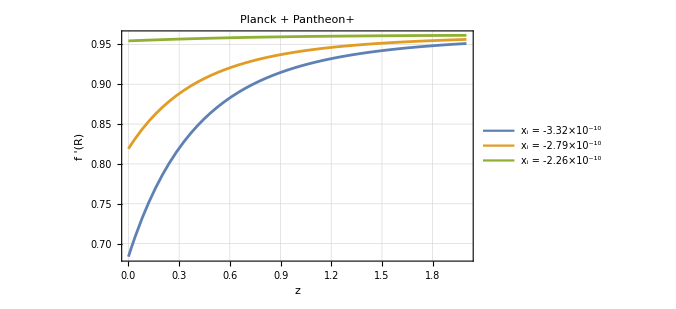

```mathematica
MakeFPlot[viablePlanckDatasets[[2]] ,Om0MeanData[viablePlanckDatasets[[2]] ]]
```

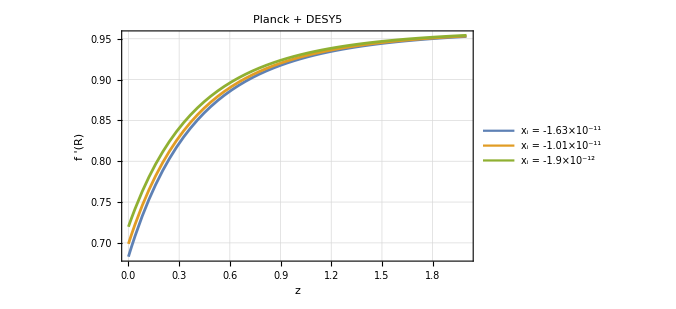

```mathematica
MakeFPlot[viablePlanckDatasets[[3]] ,Om0MeanData[viablePlanckDatasets[[3]] ]]
```

```mathematica
FEndpointTable[datasets_List,Om0Func_]:=Module[{rows},rows=Flatten[Table[Module[{sols},sols=SortedSols[dataset];
Table[Module[{F,zi},F=FOfz[dataset,s,Om0Func[dataset]];
zi=Lookup[s,"zinitial",1000];
{dataset,s["xi"],F[0],zi,F[zi]}],{s,sols}]],{dataset,datasets}],1];
Grid[Prepend[rows,Style[#,Bold]&/@{"Dataset",Subscript["x","i"],"F(0)",Subscript["z","init"],Row[{"F(",Subscript["z","init"],")"}]}],Frame->All,Alignment->Left,Background->{None,{RGBColor[0.9,0.9,0.9],None}},ItemStyle->Directive[FontSize->11],Spacings->{1.2,0.8}]];
```

```mathematica
viablePlanckDatasets={"Planck + Pantheon+","Planck + DESY5","Planck + Union3 + Pantheon+ + DESY5"}
```

{Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
FEndpointTable[viablePlanckDatasets,Om0MeanData]
```

Dataset | x_i | F(0) | z_init | F(z_init)
Planck + Pantheon+ | -3.32041410884742971693977976603×10^-10 | 0.683635 | 1000 | 0.962347
Planck + Pantheon+ | -2.78928963164302874458399799049×10^-10 | 0.818997 | 1000 | 0.962347
Planck + Pantheon+ | -2.25816515443862751373427479212×10^-10 | 0.95437 | 1000 | 0.962347
Planck + DESY5 | -1.63024183583509632063635617462×10^-11 | 0.683107 | 1000 | 0.963041
Planck + DESY5 | -1.01283885211152118649253952945×10^-11 | 0.698806 | 1000 | 0.963041
Planck + DESY5 | -1.896348738134205768108816312×10^-12 | 0.719734 | 1000 | 0.963041
Planck + Union3 + Pantheon+ + DESY5 | -6.54714820176889753734985640107×10^-10 | 0.682865 | 1000 | 0.962493
Planck + Union3 + Pantheon+ + DESY5 | -6.03019872836804218528227019896×10^-10 | 0.814803 | 1000 | 0.962493
Planck + Union3 + Pantheon+ + DESY5 | -5.51324925496718579923891830557×10^-10 | 0.94674 | 1000 | 0.962493

#### Plotting with source matching values added

```mathematica
MakeFPlotSM[dataset_,model_String,zMax_:2]:=Module[{sols,colors,Om0mean,Om0sm,curvesMean,curvesSM},sols=SortedSols[dataset];
colors=ColorData[97,"ColorList"][[1;;Length[sols]]];
Om0mean=Om0MeanData[dataset];
Om0sm=Om0SourceMatch[model,dataset];
curvesMean=Table[FOfz[dataset,s,Om0mean][z],{s,sols}];
curvesSM=Table[FOfz[dataset,s,Om0sm][z],{s,sols}];
Plot[Evaluate[Join[curvesMean,curvesSM]],{z,0,zMax},PlotStyle->Join[colors,Directive[#,Dashed,Thickness[0.002]]&/@colors],PlotLegends->Placed[Column[{LineLegend[colors,XiLabel/@sols,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],LineLegend[{Directive[Gray],Directive[Gray,Dashed,Thickness[0.002]]},{Row[{"Ω_m0 = ",NumberForm[N@Om0mean,5]," (MCMC)"}],Row[{"Ω_m0 = ",NumberForm[N@Om0sm,5]," (source match)"}]},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)]}],{0.78,0.35}],Frame->True,FrameLabel->{"z","f '(R)"},PlotLabel->Style[dataset],GridLines->Automatic,PlotRange->All,ImageSize->600]];
```

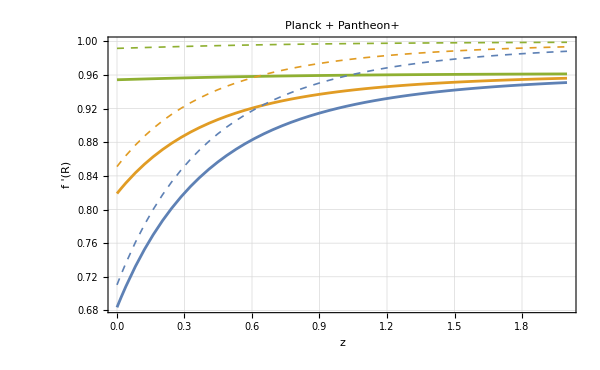

```mathematica
MakeFPlotSM[viablePlanckDatasets[[1]], "Model 3"]
```

```mathematica
viablePlanckDatasets[[2]]
```

Planck + DESY5

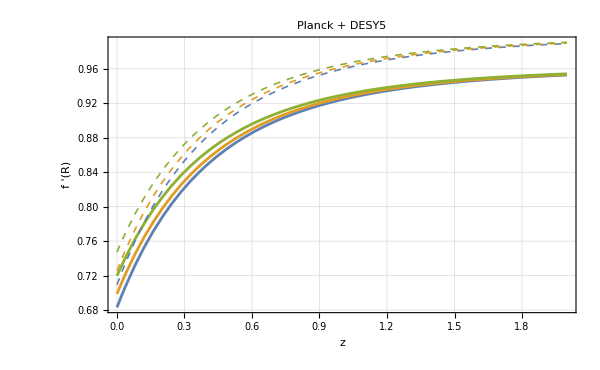

```mathematica
MakeFPlotSM[viablePlanckDatasets[[2]], "Model 3"]
```

```mathematica
viablePlanckDatasets[[3]]
```

Planck + Union3 + Pantheon+ + DESY5

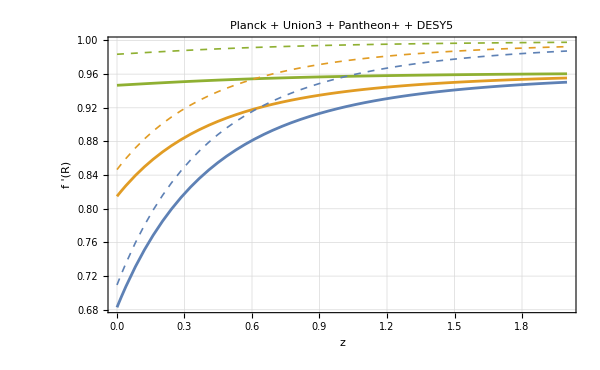

```mathematica
MakeFPlotSM[viablePlanckDatasets[[3]], "Model 3"]
```

```mathematica
FEndpointTableSM[datasets_List,model_String:"Model 3"]:=Module[{rows},rows=Flatten[Table[Module[{sols,Om0mean,Om0sm},sols=SortedSols[dataset];
Om0mean=Om0MeanData[dataset];
Om0sm=Om0SourceMatch[model,dataset];
Table[Module[{Fmean,Fsm,zi},Fmean=FOfz[dataset,s,Om0mean];
Fsm=FOfz[dataset,s,Om0sm];
zi=Lookup[s,"zinitial",1000];
{dataset,ScientificForm[N@s["xi"],3],NumberForm[N@Fmean[0],6],NumberForm[N@Fmean[zi],6],NumberForm[N@Fsm[0],6],NumberForm[N@Fsm[zi],6]}],{s,sols}]],{dataset,datasets}],1];
Grid[Prepend[rows,Style[#,Bold]&/@{"Dataset",Subscript["x","i"],"F(0) [MCMC]",Row[{"F(",Subscript["z","i"],") [MCMC]"}],"F(0) [SM]",Row[{"F(",Subscript["z","i"],") [SM]"}]}],Frame->All,Alignment->Left,Background->{None,{RGBColor[0.9,0.9,0.9],None}},ItemStyle->Directive[FontSize->11],Spacings->{1.2,0.8}]];
```

```mathematica
FEndpointTableSM[viablePlanckDatasets]
```

Dataset | x_i | F(0) [MCMC] | F(z_i) [MCMC] | F(0) [SM] | F(z_i) [SM]
Planck + Pantheon+ | -3.32×10^-10 | 0.683635 | 0.962347 | 0.710383 | 1.
Planck + Pantheon+ | -2.79×10^-10 | 0.818997 | 0.962347 | 0.851042 | 1.
Planck + Pantheon+ | -2.26×10^-10 | 0.95437 | 0.962347 | 0.991711 | 1.
Planck + DESY5 | -1.63×10^-11 | 0.683107 | 0.963041 | 0.709323 | 1.
Planck + DESY5 | -1.01×10^-11 | 0.698806 | 0.963041 | 0.725624 | 1.
Planck + DESY5 | -1.9×10^-12 | 0.719734 | 0.963041 | 0.747356 | 1.
Planck + Union3 + Pantheon+ + DESY5 | -6.55×10^-10 | 0.682865 | 0.962493 | 0.709475 | 1.
Planck + Union3 + Pantheon+ + DESY5 | -6.03×10^-10 | 0.814803 | 0.962493 | 0.846554 | 1.
Planck + Union3 + Pantheon+ + DESY5 | -5.51×10^-10 | 0.94674 | 0.962493 | 0.983633 | 1.

## Perturbation Analysis

#### Reading in

```mathematica
ClearAll[q,j,s,l,h,x,Ω,Δ,ℛhat,w,khat]
```

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/Background analysis results"];
Get["qSolAllSets.mx"];
Get["ESolAllSets.mx"]; 
Get["xOmegaSolAllSets3.mx"];
Get["cosmo_pert_equations.mx"];
SetDirectory@NotebookDirectory[];
```

```mathematica
CosmoDeltaeqnSave
CosmoReqnSave
```

Δ[z] (khat^2 w (1+z)^2+3 Eh[z]^2 (2 w q[z]+2 w x[z]-(1+w) Ω[z]))-1/(6 Eh[z]^2 (2-j[z]+q[z])^2)(1+w) ℛhat[z] (-khat^2 (1+z)^2 (-2+j[z]-q[z]) x[z]-3 Eh[z]^2 (j[z]^2-8 x[z]-s[z] x[z]-q[z]^2 (1+2 x[z])+6 Ω[z]+6 w Ω[z]+j[z] (-2+(1+q[z]) x[z]-3 (1+w) Ω[z])+q[z] (-2-11 x[z]+3 (1+w) Ω[z])))-((1+w) (1+z) x[z] ℛhat'[z])/(2 (-2+j[z]-q[z]))+((1+z) Eh[z]^2 (2+q[z])+(1+z) Eh[z]^2 (-2+3 w+x[z])) Δ'[z]+(1+z)^2 Eh[z]^2 Δ''[z]==0

-(6 Eh[z]^2 (-2+j[z]-q[z]) Δ[z] (-4 w-4 w q[z]-8 w x[z]+Ω[z]+4 w Ω[z]+3 w^2 Ω[z]))/((1+w) (1+z)^2 x[z])+ℛhat[z] (khat^2/Eh[z]^2+1/((1+z)^2 (2-j[z]+q[z])^2 x[z])(2 q[z]^4 (2+x[z])+q[z]^2 (128+133 x[z]+4 s[z] (1+x[z])-63 Ω[z]-54 w Ω[z]+9 w^2 Ω[z])+q[z]^3 (44+22 x[z]-6 (1+w) Ω[z])+j[z]^2 ((11+5 q[z]) x[z]+3 (-1+2 w+3 w^2) Ω[z])+2 (24+(48+l[z]) x[z]+s[z]^2 x[z]+6 (-7-4 w+3 w^2) Ω[z]+2 s[z] (2+8 x[z]-3 (1+w) Ω[z]))+q[z] (136+(206+l[z]) x[z]+36 (-4-3 w+w^2) Ω[z]+6 s[z] (2+6 x[z]-(1+w) Ω[z]))-j[z] (24+4 q[z]^3+34 x[z]+l[z] x[z]-48 Ω[z]-12 w Ω[z]+36 w^2 Ω[z]+2 q[z] (28+2 s[z]+11 x[z]-27 Ω[z]-18 w Ω[z]+9 w^2 Ω[z])+s[z] (4+4 x[z]-6 (1+w) Ω[z])-q[z]^2 (-36+5 x[z]+6 (1+w) Ω[z]))))+((q[z]^2 (4+x[z])+j[z] (-4+q[z] (-4+x[z])-3 x[z]+6 Ω[z]+6 w Ω[z])+q[z] (12+17 x[z]-6 (1+w) Ω[z])+2 (4+(9+s[z]) x[z]-6 (1+w) Ω[z])) ℛhat'[z])/((1+z) (-2+j[z]-q[z]) x[z])-(6 (-1+w) Eh[z]^2 (-2+j[z]-q[z]) Δ'[z])/((1+w) (1+z))+ℛhat''[z]==0

### Rewriting the equations in solvable form + dust

```mathematica
(* The rhat equation has coefficients which are very small - will give issues with NDSolve - Solution: multiply through by x[z] to remove close to singularity coeffs*)
```

```mathematica
(*multiply the R equation through by x[z],collect per-coefficient*)
ReqnSolve=Cancel[CosmoReqnSave[[1]]*x[z]]==0;
```

```mathematica
Denominator[Together[ReqnSolve[[1]]]]
```

(1+w) (1+z)^2 Eh[z]^2 (-2+j[z]-q[z])^2

```mathematica
(*Checking the equation is still correct*)
(*Symbolically*)
Together[ReqnSolve[[1]]-x[z]*CosmoReqnSave[[1]]]
```

0

```mathematica
(*Numerically*)rules={z->0,w->0.2,khat->1.5,q[z]->0.4,j[z]->1.1,s[z]->0.3,l[z]->0.05,x[z]->-0.002,Ω[z]->0.9,Δ[z]->1.2,ℛhat[z]->0.8,Derivative[1][Δ][z]->0.5,Derivative[2][Δ][z]->0.1,Derivative[1][ℛhat][z]->0.3,Derivative[2][ℛhat][z]->0.05,Eh[z]->2.5};
(ReqnSolve[[1]]/. rules)-(x[z]*CosmoReqnSave[[1]]/. rules)
rules={z->100,w->0.2,khat->1.5,q[z]->0.4,j[z]->1.1,s[z]->0.3,l[z]->0.05,x[z]->-0.002,Ω[z]->0.9,Δ[z]->1.2,ℛhat[z]->0.8,Derivative[1][Δ][z]->0.5,Derivative[2][Δ][z]->0.1,Derivative[1][ℛhat][z]->0.3,Derivative[2][ℛhat][z]->0.05,Eh[z]->2.5};
(ReqnSolve[[1]]/. rules)-(x[z]*CosmoReqnSave[[1]]/. rules)
```

-6.39488×10^-14

-4.33681×10^-18

```mathematica
ReqnSolveDust=ReqnSolve/.w->0;
DeltaeqnSolveDust =CosmoDeltaeqnSave/.w->0;
```

### Modules to solve the DE’s

#### Building cosmo variables

```mathematica
BuildCosmographyExprs[model_String,dataset_String]:=Module[{q0Val,j0Val,epsVal,jExpr,qpExpr,sExpr,lExpr,jpExpr,spExpr},
q0Val=allParams[model,dataset,"q0","mean"];
j0Val=allParams[model,dataset,"j0","mean"];
epsVal=EpsFast[model,q0Val,j0Val];

jExpr=jModelMap[model][z]/. ϵ->epsVal;
qpExpr=Solve[dq, q'[z]][[1,1,2]]/.j[z]->jExpr;(*q'(z) eliminated analytically via dq*)

jpExpr=D[jExpr,z]/.q'[z]->qpExpr;

sExpr=Solve[dj,s[z]][[1,1,2]]/.j'[z]->jpExpr/.j[z]->jExpr/.q'[z]->qpExpr//Simplify;
spExpr=D[sExpr,z]/.q'[z]->qpExpr;
lExpr=Solve[ds,l[z]][[1,1,2]]/. s'[z]->spExpr/. s[z]->sExpr//Simplify;

sExpr=N[Cancel[Together[Rationalize[sExpr,0]]]];
lExpr=N[Cancel[Together[Rationalize[lExpr,0]]]];

<|"eps"->epsVal,"q0"->q0Val,"j0"->j0Val,"j"->jExpr,"s"->sExpr,"l"->lExpr|>];
```

```mathematica
cgAssoc=Association[Table[model->Association[Table[dataset->BuildCosmographyExprs[model,dataset],{dataset,viablePlanckDatasets}]],{model,{"Model 1","Model 2","Model 3"}}]];
```

```mathematica
cgAssoc["Model 3", viablePlanckDatasets[[1]],"j"]
```

1+0.0468939 (-1/2+q[z])

#### Background source matching Ω_m(z)

```mathematica
OmegaMatterSM[model_String,dataset_String]:=With[
{Om0=Om0SourceMatch[model,dataset],
EhFn=EAssocByModel[model][dataset]},
Function[zz,Om0 (1+zz)^3/EhFn[zz]^2]];
```

```mathematica
OmegamAssoc=<|"Model 3"->Association[Table[dataset->OmegaMatterSM["Model 3",dataset],{dataset,viablePlanckDatasets}]]|>;
(*Cant use the Omega_m source matching (Amatch) for model 1 and 2*)
```

```mathematica
Table[Module[{store,Omm,bg,zi},store=bgRun["Model 3"]["bgResults"][dataset];
Omm=OmegamAssoc["Model 3"][dataset];
bg=store[First@Keys[store]];
zi=bg["zinitial"];
{dataset,Om0SourceMatch["Model 3",dataset],Omm[zi],bg["Ωi"],Omm[zi]-bg["Ωi"]}],{dataset,viablePlanckDatasets}]//TableForm
```

Planck + Pantheon+ | 0.326202 | 1. | 0.999999997260855755243369458185 | -2.16553×10^-8
Planck + DESY5 | 0.321029 | 1. | 0.999999998266208223185458336957 | -1.24619×10^-8
Planck + Union3 + Pantheon+ + DESY5 | 0.328908 | 1. | 0.999999996366487176047144203039 | -2.15755×10^-8

#### Perturbation system

```mathematica
BuildPertSystem[model_String,dataset_String,idx_Integer,khatVal_?NumericQ]:=Module[{store,cg,jE,sE,lE,bg,label,xFn,OmFn,qFn,EhFn,cgRules,bgRules},store=bgRun[model]["bgResults"][dataset];
cg=cgAssoc[model][dataset] (*cosmographic (s,l) functions*);
{jE,sE,lE}=cg/@{"j","s","l"};
label=Keys[store][[idx]];(*idx associates which initial condition on x is being used*)bg=store[label] (*x and Omega functions*);

xFn=bg["x"];
OmFn=bg["Ω"];
qFn=bg["q"];
EhFn=EAssocByModel[model][dataset];

cgRules={j[z]->jE,s[z]->sE,l[z]->lE};(*cosmography first: j,s,l still contain free q[z]*)
bgRules={q[z]->qFn[z],x[z]->xFn[z],Ω[z]->OmFn[z],Eh[z]->EhFn[z],khat->khatVal};(*then bind the interpolants*)
<|"eqR"->(ReqnSolveDust/. cgRules/. bgRules),
"eqD"->(DeltaeqnSolveDust/. cgRules/. bgRules),
"label"->label,"khat"->khatVal,"xi"->bg["xi"],"Ωi"->bg["Ωi"],"zinitial"->bg["zinitial"],"eps"->cg["eps"],"q0"->cg["q0"],"j0"->cg["j0"],"Ehi"->EhFn[bg["zinitial"]]|>];
```

#### Initial conditions

Following 21 cm paper: (2606.03729v1)
Δ(1000)=10^-5, 		Δ'(1000)=-9.99*10^-9

At high redshift indistuinguishable from GR -->
ℛhat = 3(1-3w) E^2 Ω_mΔ,		ℛhat ‘ = 3(1-3w) E^2 Ω_m Δ/(1+z)[3+(1+z) Δ'/Δ]

We can only do this if Omega_m(z) matches GR so then we need to use the source matching Omega_m0 - not jess’s value.

```mathematica
(*Checking that Rhat is correct in GR limit*)
Simplify[grLimit=ReqnSolveDust[[1]]==0/. {x[z]->0,q[z]->1/2,j[z]->1,s[z]->-7/2,l[z]->35/2,Ω[z]->1}//Cancel, z>=0]
```

ℛhat[z]==3 Eh[z]^2 Δ[z]

```mathematica
(*This is only true for Omega(z)->1*)
```

```mathematica
BuildPertICs[model_String,dataset_String,sys_Association,DeltaIn_:10^-5,γ_:6/11]:=Module[
{zi,Omi,Ehi,DeltaPrimei,Ri,RPrimei},
zi=sys["zinitial"];
Ehi=sys["Ehi"];
Omi=OmegamAssoc[model][dataset][zi] (*Source matching Ωm(z)*);

DeltaPrimei=-DeltaIn/(1+zi)Omi^γ; (*Derived from definition of S eqn 11 of 2606.03729v1*)

Ri=3 Ehi^2 Omi DeltaIn;
RPrimei=Ri/(1+zi)(3+(1+zi)DeltaPrimei/DeltaIn);
<|"Δi"->DeltaIn,"Δprimei"->DeltaPrimei,"Ri"->Ri,"Rprimei"->RPrimei,"zi"->zi,"Ehi"->Ehi,"Ωmi"->Omi|>];
```

```mathematica
sys=BuildPertSystem["Model 3","Planck + Pantheon+",1,29.98];
ics=BuildPertICs["Model 3","Planck + Pantheon+",sys]
```

<|Δi→1/100000,Δprimei→-9.99001×10^-9,Ri→9815.44,Rprimei→19.6113,zi→1000,Ehi→18088.2,Ωmi→1.|>

#### Perturbation solver +results

```mathematica
(*Scale conversion: khat=k c/(a0 H0),H0=100 h km/s/Mpc. With k in h/Mpc,the h cancels: khat=k[h/Mpc]*c/100=2997.92*k[h/Mpc] *)
c=3*10^5;   (*c in km/s *)
kPhys={0.01,0.03,0.1,0.2};              (*h Mpc^-1*)
khatVals=c/100 kPhys;                    (*{29.98,89.94,299.79,599.58}*)
kLabels=Row[{"k = ",#," h Mpc",Superscript["",-1]}]&/@kPhys;
```

```mathematica
SolvePerturbations[model_String,dataset_String,idx_Integer,khatVal_?NumericQ]:=Module[{sys,ics,zi,sol,DeltaFn,RFn},sys=BuildPertSystem[model,dataset,idx,khatVal];
ics=BuildPertICs[model,dataset,sys];
zi=ics["zi"];
sol=Quiet[NDSolve[{sys["eqD"],sys["eqR"],Δ[zi]==ics["Δi"],Δ'[zi]==ics["Δprimei"],ℛhat[zi]==ics["Ri"],ℛhat'[zi]==ics["Rprimei"]},{Δ,ℛhat},{z,0,zi}],{NDSolve::ndsz,NDSolve::mxst,NDSolve::ndcf,NDSolve::precw}];
If[!MatchQ[sol,{{__Rule}}],Return[$Failed]];
DeltaFn=Δ/. sol[[1]];
RFn=ℛhat/. sol[[1]];
<|"Δ"->DeltaFn,"ℛhat"->RFn,"domainEnd"->DeltaFn["Domain"][[1,1]],"label"->sys["label"],"khat"->khatVal,"xi"->sys["xi"],"ics"->ics|>];
```

```mathematica
SolveAllPerturbations[model_String,datasets_List,khatList_List,nIdx_:3]:=Association[Table[dataset->Association[Table[Module[{label},label=Keys[bgRun[model]["bgResults"][dataset]][[i]];
label->Association[MapThread[Function[{kp,khv},Module[{r},r=SolvePerturbations[model,dataset,i,khv];
If[r===$Failed,Print[Style[Row[{dataset,"  |  ",label,"  |  k = ",kp," h/Mpc  (khat = ",khv,"):  FAILED"}],Red]]];
kp->r]],{kPhys,khatList}]]],{i,nIdx}]],{dataset,datasets}]];
```

```mathematica
(*pertResults3=SolveAllPerturbations["Model 3",viablePlanckDatasets,khatVals];
SetDirectory@NotebookDirectory[];
DumpSave["Perturbation_solns_Model_3.mx",pertResults3]*)
```

```mathematica
SetDirectory@NotebookDirectory[];
Get["Perturbation_solns_Model_3.mx"]
```

```mathematica
With[{d=First[viablePlanckDatasets],lab=Keys[bgRun["Model 3"]["bgResults"][First@viablePlanckDatasets]][[1]]},{Head[pertResults3[d][lab][First@kPhys]],pertResults3[d][lab][First@kPhys]}//Short[#,8]&]
```

{Association,<|Δ→InterpolatingFunction[{{0., 1000.}}, <>],ℛhat→InterpolatingFunction[{{0., 1000.}}, <>],domainEnd→0.,label→x_i = -3.32×10^-10,khat→30.,xi→-3.32041410884742971693977976603×10^-10,ics→<|Δi→1/100000,Δprimei→-9.99001×10^-9,Ri→9815.44,Rprimei→19.6113,zi→1000,Ehi→18088.2,Ωmi→1.|>|>}

### Results

#### Density contrast plots

```mathematica
kLabels=Row[{"k = ",#," h Mpc",Superscript["",-1]}]&/@kPhys;
```

```mathematica
PlotNormalisedD[dataset_String,label_]:=Module[{byK,curves},
byK=pertResults3[dataset][label];
curves=Table[byK[kp]["Δ"][z]/byK[kp]["Δ"][0],{kp,kPhys}];
LogLinearPlot[Evaluate[curves],{z,0,zPlot},PlotLegends->Placed[LineLegend[Automatic,kLabels,LegendFunction->(Framed[#,RoundingRadius->0,FrameStyle->GrayLevel[0.5]]&),LabelStyle->{FontSize->10}],{0.2,0.3}],PlotRange->All,Frame->True,FrameLabel->{"z","D(z)"},PlotLabel->Row[{dataset,"   ",label}],ImageSize->500]];
```

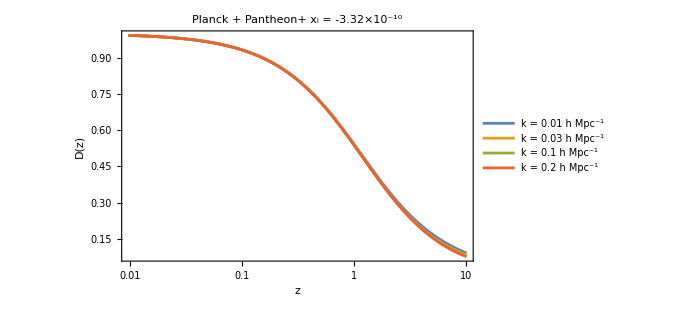

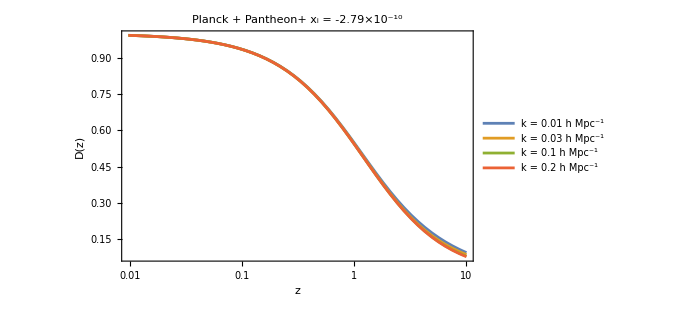

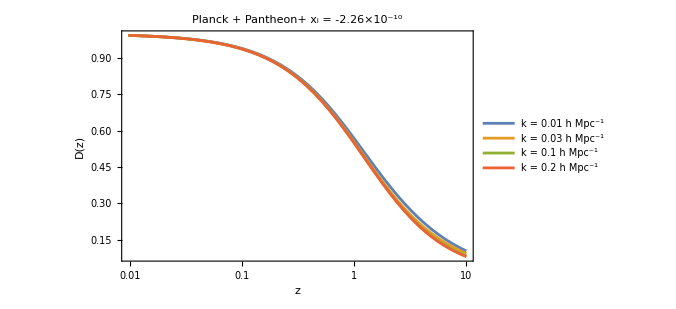

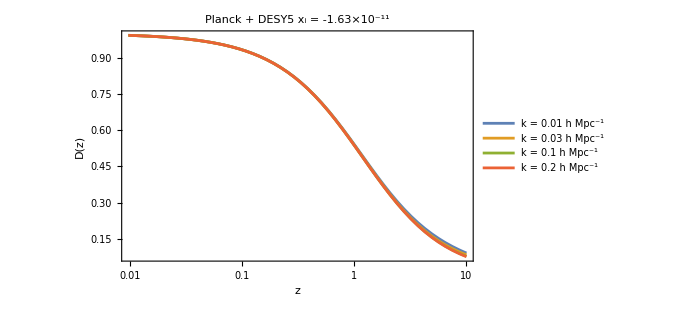

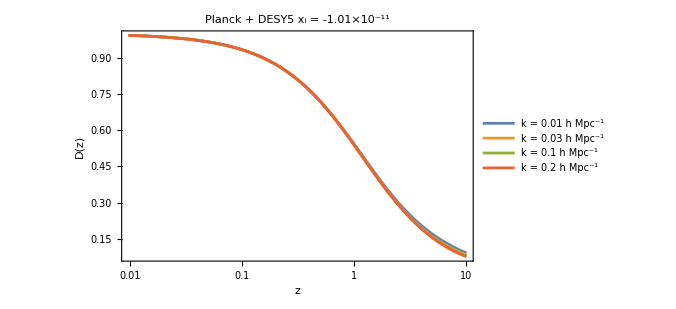

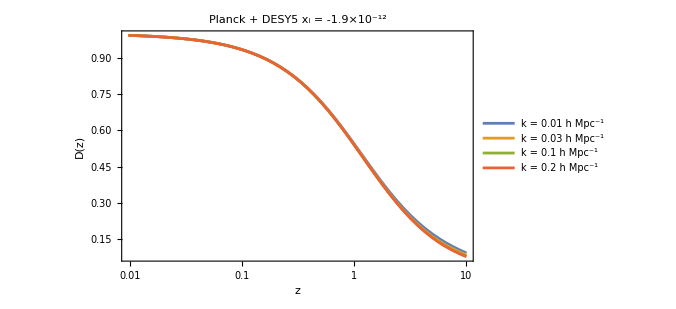

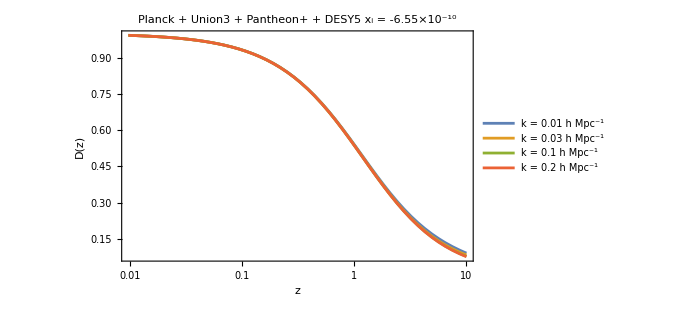

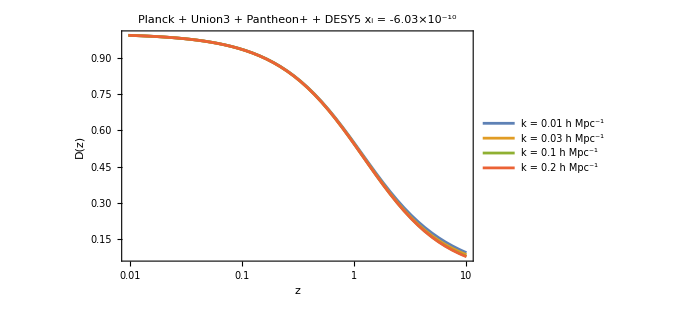

```mathematica
Do[Print[PlotNormalisedD[dataset,label]],{dataset,viablePlanckDatasets},{label,Keys[pertResults3[dataset]]}]
```

```mathematica
DTableAtZ[zval_:10]:=Module[{rows},rows=Flatten[
Table[Module[
{byK,vals},
byK=pertResults3[dataset][label];
vals=Table[byK[kp]["Δ"][zval]/byK[kp]["Δ"][0],{kp,kPhys}];
Join[{dataset,label},NumberForm[#,6]&/@vals]],
{dataset,viablePlanckDatasets},{label,Keys[pertResults3[dataset]]}],1];
Grid[Prepend[rows,Style[#,Bold]&/@Join[{"Dataset",Subscript["x","i"]},ToString[#]<>" h/Mpc"&/@kPhys]],Frame->All,Alignment->Left,ItemStyle->Directive[FontSize->11]]];

DTableAtZ[10]
```

Dataset | x_i | 0.01 h/Mpc | 0.03 h/Mpc | 0.1 h/Mpc | 0.2 h/Mpc
Planck + Pantheon+ | x_i = -3.32×10^-10 | 0.0910427 | 0.0833672 | 0.0776452 | 0.0760594
Planck + Pantheon+ | x_i = -2.79×10^-10 | 0.0944639 | 0.0862794 | 0.079577 | 0.0775102
Planck + Pantheon+ | x_i = -2.26×10^-10 | 0.103596 | 0.0933759 | 0.0838097 | 0.0801839
Planck + DESY5 | x_i = -1.63×10^-11 | 0.0913415 | 0.0838223 | 0.0779354 | 0.076188
Planck + DESY5 | x_i = -1.01×10^-11 | 0.0917034 | 0.0841468 | 0.0781659 | 0.0763652
Planck + DESY5 | x_i = -1.9×10^-12 | 0.0922073 | 0.0846027 | 0.0784888 | 0.0766118
Planck + Union3 + Pantheon+ + DESY5 | x_i = -6.55×10^-10 | 0.0908596 | 0.0831087 | 0.0775116 | 0.0760235
Planck + Union3 + Pantheon+ + DESY5 | x_i = -6.03×10^-10 | 0.093975 | 0.0856604 | 0.0791715 | 0.0773058
Planck + Union3 + Pantheon+ + DESY5 | x_i = -5.51×10^-10 | 0.100512 | 0.090366 | 0.0817903 | 0.0790107

### Growth function

```mathematica
SFunc[dataset_String,lab_,kp_,z_?NumericQ]:=With[{DeltaFn=pertResults3[dataset][lab][kp]["Δ"]},-(1+z) DeltaFn'[z]/DeltaFn[z]];
```

```mathematica
PlotSAllModes[dataset_String,zmax_:6]:=Module[{labels,dashings,curves,styles,legFn,legend},
labels=Keys[pertResults3[dataset]];
dashings={Dashing[{}],Dashing[{0.02,0.015}],Dashing[{0.005,0.01}]};
curves=Flatten[Table[SFunc[dataset,lab,kp,zz],{lab,labels},{kp,kPhys}]];
styles=Flatten[Table[Directive[ColorData[97][j],dashings[[i]]],{i,Length[labels]},{j,Length[kPhys]}],1];
legFn=Framed[#,RoundingRadius->0,FrameStyle->GrayLevel[0.5],Background->GrayLevel[1,0.9],FrameMargins->4]&;
legend=Column[{LineLegend[ColorData[97]/@Range[Length[kPhys]],kLabels,LegendFunction->legFn,LabelStyle->{FontSize->9},LegendMargins->0],LineLegend[Directive[Black,#]&/@dashings,labels,LegendFunction->legFn,LabelStyle->{FontSize->9},LegendMargins->0]},Spacings->0.3];
Plot[Evaluate[curves],{zz,0,zmax},PlotStyle->styles,PlotLegends->Placed[legend,{0.83,0.32}],GridLines->{None,{1}},GridLinesStyle->Directive[Gray,Dashed,Thickness[0.003]],Frame->True,FrameLabel->{"z","S(z)"},PlotRange->All,PlotLabel->dataset,ImageSize->500]];
```

```mathematica
SLegend[dataset_String]:=Module[{labels,dashings},labels=Keys[pertResults3[dataset]];
dashings={Dashing[{}],Dashing[{0.02,0.015}],Dashing[{0.005,0.01}]};
Column[{LineLegend[ColorData[97]/@Range[Length[kPhys]],kLabels,LegendFunction->"Frame",LegendLabel->"scale",LabelStyle->{FontSize->9}],LineLegend[Directive[Black,#]&/@dashings,labels,LegendFunction->"Frame",LegendLabel->"initial condition",LabelStyle->{FontSize->9}]}]];
```

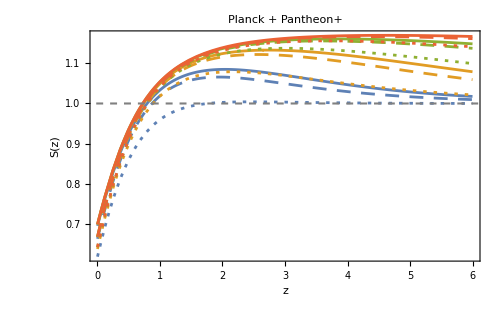

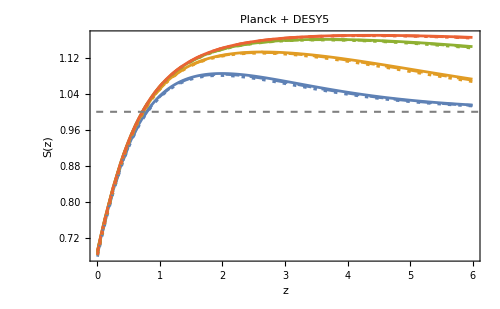

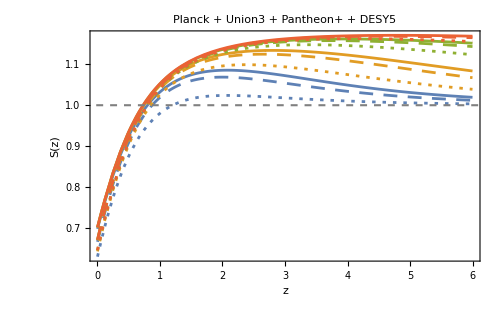

```mathematica
Do[Print[PlotSAllModes[dataset]],{dataset,viablePlanckDatasets}]
```

#### High z

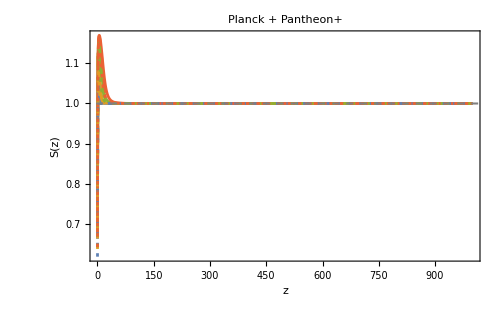

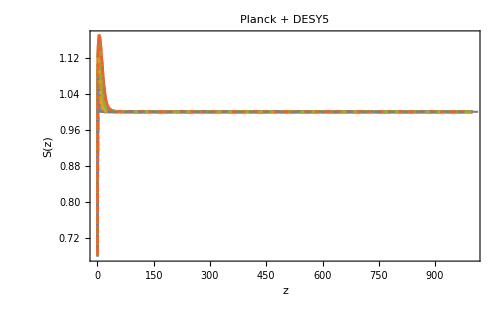

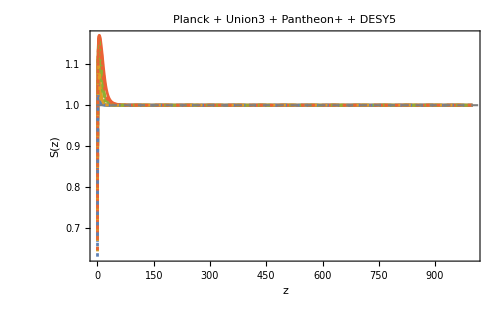

```mathematica
Do[Print[PlotSAllModes[dataset,1000]],{dataset,viablePlanckDatasets}]
```

#### Growth index parameter

```mathematica
GammaFn[dataset_,label_,kp_]:=With[
{DeltaFn=pertResults3[dataset][label][kp]["Δ"],OmmFn=OmegamAssoc["Model 3"][dataset]},
Function[z,Log[-(1+z) DeltaFn'[z]/DeltaFn[z]]/Log[OmmFn[z]]]];
```

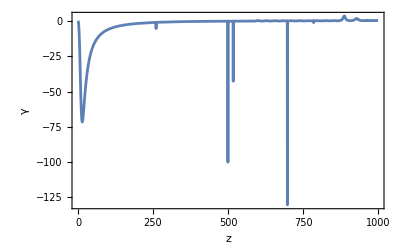

```mathematica
gf=GammaFn["Planck + DESY5",Keys[pertResults3[viablePlanckDatasets[[2]]]][[1]],0.1];
Plot[gf[z],{z,0.,1000},PlotRange->All,Frame->True,FrameLabel->{"z","γ"}]
```

```mathematica
N[6/11]
```

0.545455

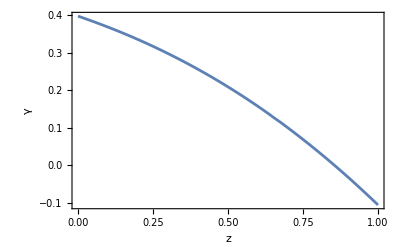

```mathematica
gf=GammaFn[viablePlanckDatasets[[3]],Keys[pertResults3[viablePlanckDatasets[[3]]]][[3]],0.03];
Plot[gf[z],{z,0.,1},PlotRange->All,Frame->True,FrameLabel->{"z","γ"}]
```

### New paramaterisation

```mathematica
QParts[model_String,dataset_String,lab_,kp_?NumericQ,zv_?NumericQ]:=Module[{bg,pr,Dl,Rh,khat,S,T,x,Om,qv,Eh,j,s,Ommat,fR,DD,M,P,τ,brk,A3,A4,d2},
bg=bgRun[model]["bgResults"][dataset][lab];
pr=pertResults3[dataset][lab][kp];
Dl=pr["Δ"];Rh=pr["ℛhat"];
khat=pr["khat"];
x=bg["x"][zv];Om=bg["Ω"][zv];
qv=bg["q"][zv];
Eh=EAssocByModel[model][dataset][zv];

{j,s}={cgAssoc[model][dataset]["j"],cgAssoc[model][dataset]["s"]}/. q[z]->qv/. z->zv;
Ommat=OmegamAssoc[model][dataset][zv];
fR=Ommat/Om;
DD=j-qv-2;
S=-(1+zv) Dl'[zv]/Dl[zv];
T=-(1+zv) Rh'[zv]/Rh[zv];
M=(khat^2 (1+zv)^2 x)/(6 DD Eh^2);
P=j^2-8 x-s x-qv^2 (1+2 x)+6 Om+j (-2+(1+qv) x-3 Om)+qv (-2-11 x+3 Om);
A3=-((khat^2 x)/(6 DD Eh^4)+P/(2 DD^2 Eh^2 (1+zv)^2));
A4=x/(2 DD Eh^2 (1+zv));
d2=(-(qv+x))/(1+zv) Dl'[zv]+(3 Om)/(1+zv)^2 Dl[zv]+A3 Rh[zv]+A4 Rh'[zv]; (*Δ'' equation*)
τ=Rh[zv]/(3 Eh^2 Ommat Dl[zv]);
brk=2 M+P/DD^2+(x T)/DD;
<|"S"->S,"T"->T,"τ"->τ,"M"->M,"fR"->fR,"Ωm"->Ommat,"d2"->d2,"Qgrav"->2/fR,"Qcurv"->-τ brk,"Q"->2/fR-τ brk|>];
```

```mathematica
QOf[model_String,dataset_String,lab_,kp_,zv_?NumericQ]:=QParts[model,dataset,lab,kp,zv]["Q"];
```

#### Confirming (numerically) equations and Q(z)

```mathematica
(*To confirm that the Q(z) above is calcualted correctly*)
PertResidual[model_String,dataset_String,lab_,kp_?NumericQ,zv_?NumericQ]:=Module[{Dl,qv,x,S,p,lhs,rhs},
Dl=pertResults3[dataset][lab][kp]["Δ"];
qv=bgRun[model]["bgResults"][dataset][lab]["q"][zv];
x=bgRun[model]["bgResults"][dataset][lab]["x"][zv];
S=-(1+zv) Dl'[zv]/Dl[zv];
p=QParts[model,dataset,lab,kp,zv];
lhs=(1+zv) Dl'[zv]/Dl[zv]+(1+zv)^2 p["d2"]/Dl[zv]+(1-qv-x) S;
rhs=(3/2) p["Ωm"] p["Q"];
Abs[lhs-rhs]/Max[Abs[lhs],Abs[rhs],$MinMachineNumber]];
```

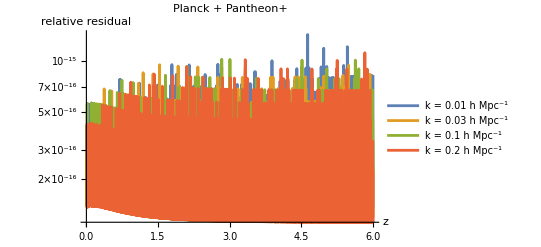
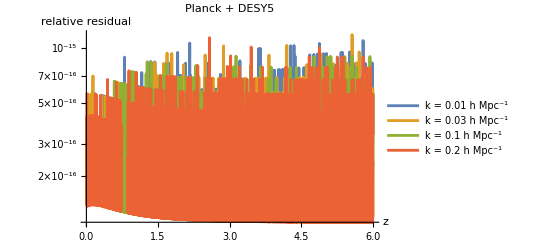
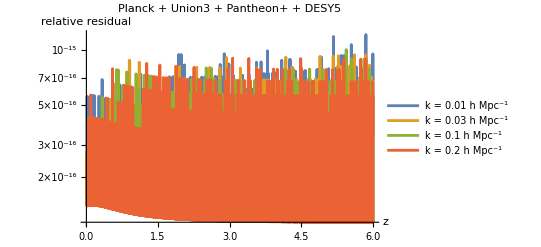

```mathematica
Table[With[{lab=First@Keys[bgRun["Model 3"]["bgResults"][dataset]]},Plot[Evaluate@Table[PertResidual["Model 3",dataset,lab,kp,zv],{kp,kPhys}],{zv,0.01,6},ScalingFunctions->"Log",PlotRange->All,PlotLegends->kLabels,AxesLabel->{"z","relative residual"},PlotLabel->dataset, ImageSize->400]],{dataset,viablePlanckDatasets}]
```

#### Q decomposition

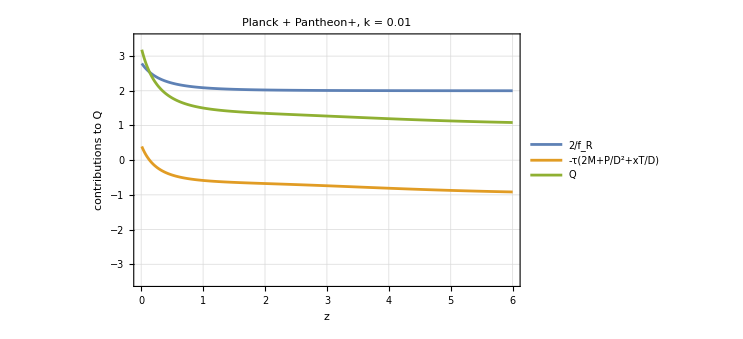
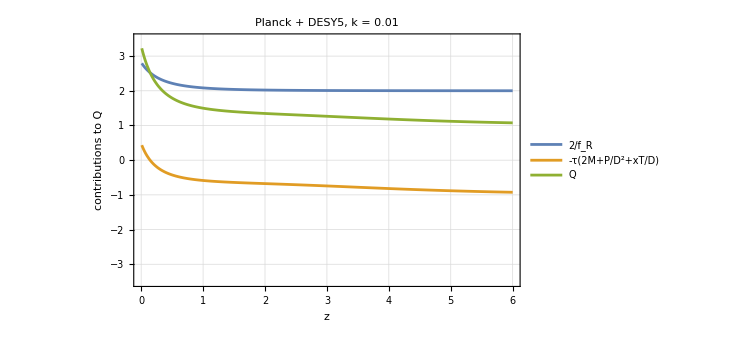
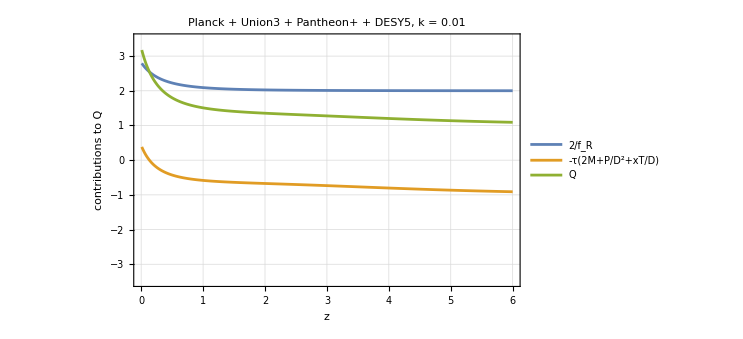

```mathematica
Table[With[{lab=First@Keys[bgRun["Model 3"]["bgResults"][dataset]],kp=First@kPhys},Plot[{QParts["Model 3",dataset,lab,kp,zv]["Qgrav"],QParts["Model 3",dataset,lab,kp,zv]["Qcurv"],QParts["Model 3",dataset,lab,kp,zv]["Q"]},{zv,0.01,6},PlotRange->{{0,6},{-3.5,3.5}},Frame->True,Axes->False,FrameLabel->{"z","contributions to Q"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],PlotLegends->Placed[LineLegend[{"2/f_R","\!\(\*RowBox[{\"-τ\", \"(\", RowBox[{\"2\", \"M\", \"+\", FractionBox[\"P\", SuperscriptBox[\"D\", \"2\"]], \"+\", FractionBox[RowBox[{\"x\", \"T\"}], \"D\"]}], \")\"}]\)","Q"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.5],RoundingRadius->0]&),LegendMarkerSize->10],{0.2,0.19}],ImageSize->550,PlotLabel->dataset<>", k = "<>ToString[kp]]],{dataset,viablePlanckDatasets}]
```

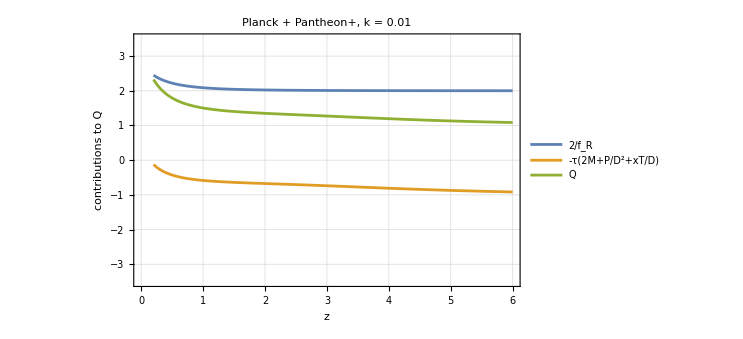
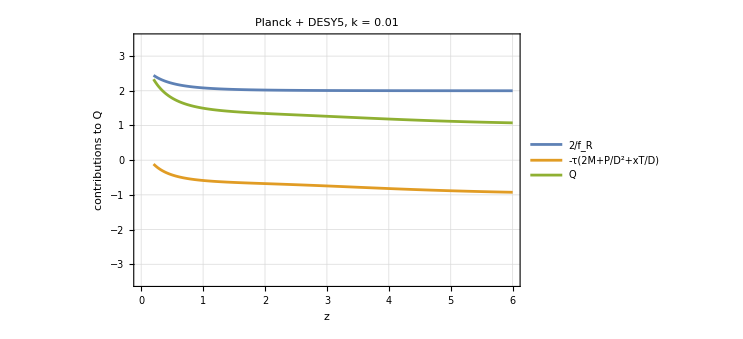
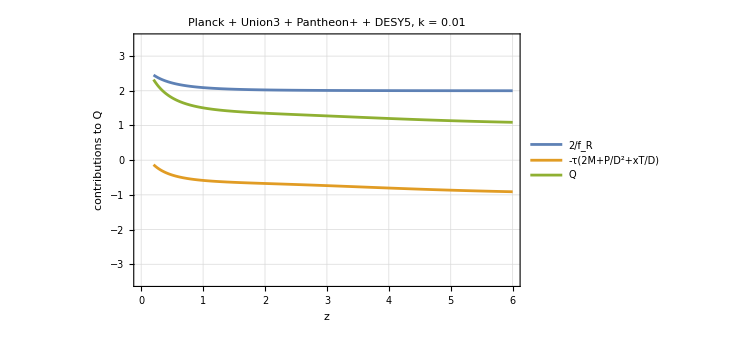

```mathematica
Table[With[{lab=First@Keys[bgRun["Model 3"]["bgResults"][dataset]],kp=First@kPhys},Plot[{QParts["Model 3",dataset,lab,kp,zv]["Qgrav"],QParts["Model 3",dataset,lab,kp,zv]["Qcurv"],QParts["Model 3",dataset,lab,kp,zv]["Q"]},{zv,0.2,6},PlotRange->{{0,6},{-3.5,3.5}},Frame->True,Axes->False,FrameLabel->{"z","contributions to Q"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],PlotLegends->Placed[LineLegend[{"2/f_R","\!\(\*RowBox[{\"-τ\", \"(\", RowBox[{\"2\", \"M\", \"+\", FractionBox[\"P\", SuperscriptBox[\"D\", \"2\"]], \"+\", FractionBox[RowBox[{\"x\", \"T\"}], \"D\"]}], \")\"}]\)","Q"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.5],RoundingRadius->0]&),LegendMarkerSize->10],{0.2,0.19}],ImageSize->550,PlotLabel->dataset<>", k = "<>ToString[kp]]],{dataset,viablePlanckDatasets}]
```

#### Plotting Q

```mathematica
kPhys
```

{0.01,0.03,0.1,0.2}

```mathematica
PlotQScales[model_String,dataset_String]:=With[{lab=First@Keys[bgRun[model]["bgResults"][dataset]]},Plot[Evaluate@Table[QParts[model,dataset,lab,kp,zv]["Q"],{kp,kPhys}],{zv,0,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"z","Q(z)"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],PlotLegends->Placed[LineLegend[kLabels,LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.7],RoundingRadius->3]&),LegendMarkerSize->20],{0.78,0.7}],ImageSize->500,PlotLabel->dataset]];
```

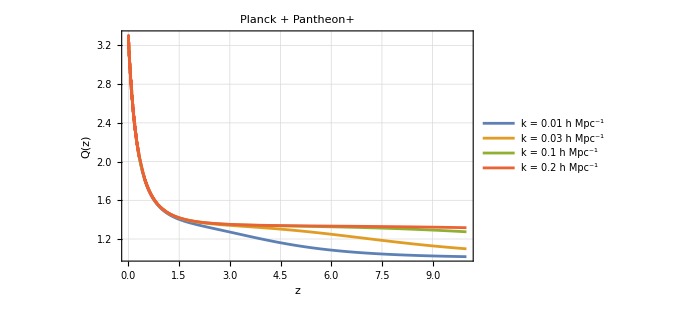
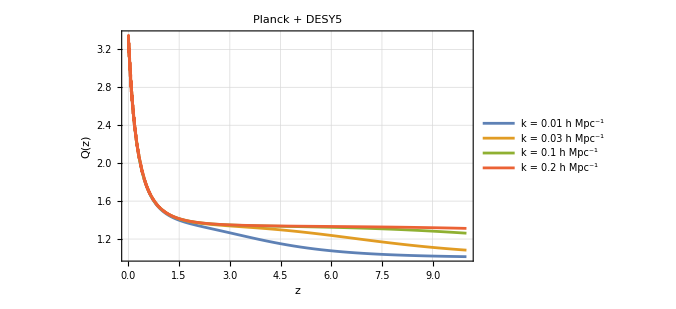
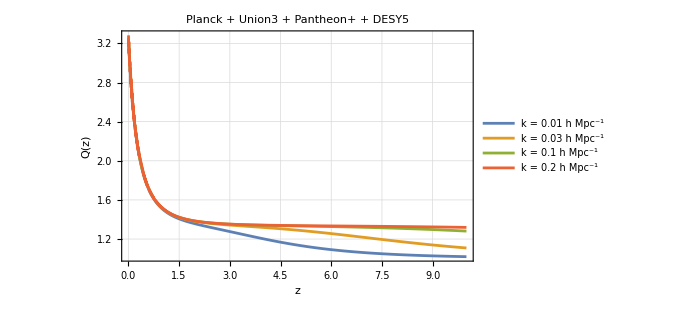

```mathematica
Table[PlotQScales["Model 3",dataset],{dataset,viablePlanckDatasets}]
```